# Método de los momentos aproximado- Normal estándar

```mathematica
SeedRandom[1234]
```

```mathematica
datos1 =  RandomVariate[NormalDistribution[0,1],10001]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9973,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

```mathematica
Extract[datos1,7615]
```

4.16036

```mathematica
datos=Delete[datos1,7615]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9972,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

### MOP DE GRADO 3

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(128 b)/3+(2048 d)/5

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(128 a)/3+(2048 c)/5

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7

```mathematica
(*Función de las diferencias al cuadrado entre los momentos poblacionales y los muestrales*)
```

```mathematica
F3[a_,b_,c_,d_]=((128 b)/3+(2048 d)/5-(Apply[Plus,datos])/10000)^2+((128 a)/3+(2048 c)/5-(Apply[Plus,datos^2])/10000)^2+((2048 b)/5+(32768 d)/7-(Apply[Plus,datos^3])/10000)^2+((2048 a)/5+(32768 c)/7-(Apply[Plus,datos^4])/10000)^2
```

(-0.992368+(128 a)/3+(2048 c)/5)^2+(-2.9755+(2048 a)/5+(32768 c)/7)^2+(0.0196627+(128 b)/3+(2048 d)/5)^2+(0.0566338+(2048 b)/5+(32768 d)/7)^2

```mathematica
Minimize[{F3[a,b,c,d],{a+4 b+16 c+64 d>0,a-4 b+4^2 c-4^3 d>0}},{a,b,c,d}]
```

{0.305632,{a→0.0261995,b→-0.00046271,c→-0.00163745,d→0.0000289149}}

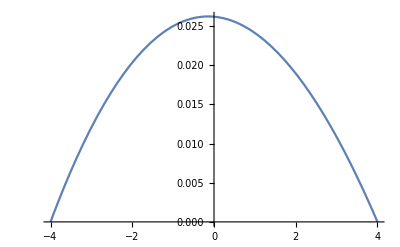

```mathematica
Plot[a+b*x+c*x^2+d*x^3/.{a->0.026199457348090045,b->-0.00046271037246538234,c->-0.0016374495425826832,d->0.000028914934557545556},{x,-4,4}]
```

```mathematica
Integrate[a+b*x+c*x^2+d*x^3/.{a->0.026199457348090045,b->-0.00046271037246538234,c->-0.0016374495425826832,d->0.000028914934557545556},{x,-4,4}]
```

0.139731

```mathematica
f3[x_]=(a+b*x+c*x^2+d*x^3)/0.1397311449678592/.{a->0.026199457348090045,b->-0.00046271037246538234,c->-0.0016374495425826832,d->0.000028914934557545556}
```

7.1566 (0.0261995-0.00046271 x-0.00163745 x^2+0.0000289149 x^3)

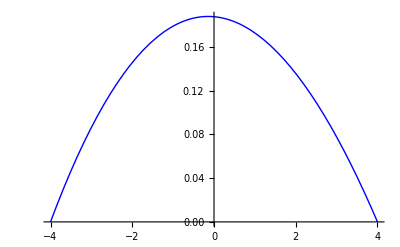

```mathematica
Plot[f3[x],{x,-4,4},PlotStyle->{Blue,Thin}]
```

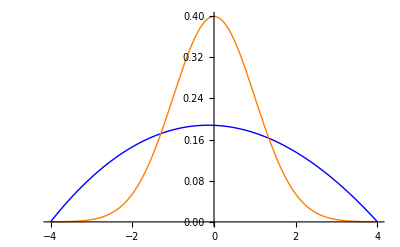

```mathematica
Plot[{f3[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Orange,Thin}}]
```

```mathematica
Solve[f3[x]==0,Reals]
```

{{x→-4.00004},{x→4.},{x→56.6299}}

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
F[x_]=(PDF[NormalDistribution[0,1],x])/0.9999366575163338
```

0.398968 ⅇ^(-x^2/2)

```mathematica
KL3= N[Integrate[F[x]*Log[F[x]/f3[x]],{x,-4,4}]]
```

0.326031

```mathematica
(*Verosimilitud*)
```

```mathematica
f3[datos]
```

{0.186127,0.187674,0.162168,0.155493,0.0985622,0.171067,0.176813,0.186787,0.187027,0.159267,0.187366,0.186597,0.174335,0.182108,9972,0.180943,0.185853,0.169812,0.187251,0.170818,0.181684,0.18595,0.170232,0.187284,0.176113,0.175483,0.184902,0.17385,0.187013}
 |  |  |  |

```mathematica
x3 = Log[f3[datos]]
```

{-1.68133,-1.67305,-1.81912,-1.86116,-2.31707,-1.7657,-1.73267,-1.67779,-1.6765,-1.83718,-1.67469,-1.6788,-1.74678,-1.70315,9972,-1.70957,-1.6828,-1.77307,-1.6753,-1.76716,-1.70549,-1.68228,-1.77059,-1.67513,-1.73663,-1.74021,-1.68793,-1.74956,-1.67658}
 |  |  |  |

```mathematica
V3=Apply[Plus,x3]
```

-17437.1

```mathematica
(*BIC*)
```

```mathematica
BIC3 = -2*V3 + 4*Log[10000]
```

34910.9

### MOP DE GRADO 5

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11

```mathematica
(*Función de la suma de las diferencias al cuadrado entre los momentos poblacionales y los muestrales*)
```

```mathematica
F5[a_,b_,c_,d_,e_,f_]=((128 b)/3+(2048 d)/5+(32768 f)/7-(Apply[Plus,datos])/10000)^2+((128 a)/3+(2048 c)/5+(32768 e)/7-(Apply[Plus,datos^2])/10000)^2+((2048 b)/5+(32768 d)/7+(524288 f)/9-(Apply[Plus,datos^3])/10000)^2+((2048 a)/5+(32768 c)/7+(524288 e)/9-(Apply[Plus,datos^4])/10000)^2+((32768 b)/7+(524288 d)/9+(8388608 f)/11-(Apply[Plus,datos^5])/10000)^2+((32768 a)/7+(524288 c)/9+(8388608 e)/11-(Apply[Plus,datos^6])/10000)^2
```

(-0.992368+(128 a)/3+(2048 c)/5+(32768 e)/7)^2+(-2.9755+(2048 a)/5+(32768 c)/7+(524288 e)/9)^2+(-14.7766+(32768 a)/7+(524288 c)/9+(8388608 e)/11)^2+(0.0196627+(128 b)/3+(2048 d)/5+(32768 f)/7)^2+(0.0566338+(2048 b)/5+(32768 d)/7+(524288 f)/9)^2+(0.355927+(32768 b)/7+(524288 d)/9+(8388608 f)/11)^2

```mathematica
(*Minimización de la función F5 sujeta a restricciones hasta que el área de la parte negativa sea menor que el 1% del área total*)
```

```mathematica
(*Restricciones iniciales: extremos positivos*)
```

```mathematica
Minimize[{F5[a,b,c,d,e,f],{a+4 b+16 c+64 d+256 e+1024 f>0,a-4 b+16 c-64 d+256 e-1024 f>0}},{a,b,c,d,e,f}]
```

{1.44062,{a→0.764744,b→-0.0107117,c→-0.165911,d→0.00230235,e→0.00799885,f→-0.000110588}}

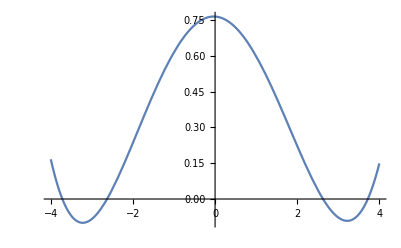

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.7647441063226019,b->-0.010711739552200053,c->-0.16591072367479623,d->0.002302348778138773,e->0.007998850699100453,f->-0.00011058813275202704},{x,-4,4}]
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5
```

a+b x+c x^2+d x^3+e x^4+f x^5

```mathematica
F51[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.7647441063226019,b->-0.010711739552200053,c->-0.16591072367479623,d->0.002302348778138773,e->0.007998850699100453,f->-0.00011058813275202704}
```

0.764744-0.0107117 x-0.165911 x^2+0.00230235 x^3+0.00799885 x^4-0.000110588 x^5

```mathematica
Solve[F51[x]==0,Reals]
```

{{x→-3.71838},{x→-2.63018},{x→2.62873},{x→3.71875},{x→72.3312}}

```mathematica
APN = -Integrate[F51[x],{x,-3.7183775854892116,-2.6301767081433063}]-Integrate[F51[x],{x,2.628734437495631,3.718750096519542}]
```

0.137972

```mathematica
AT=Integrate[F51[x],{x,-4,-3.7183775854892116}]-Integrate[F51[x],{x,-3.7183775854892116,-2.6301767081433063}]+Integrate[F51[x],{x,-2.6301767081433063,2.628734437495631}]-Integrate[F51[x],{x,2.628734437495631,3.718750096519542}]+Integrate[F51[x],{x,3.718750096519542,4}]
```

2.59137

```mathematica
APN/AT
```

0.0532431

```mathematica
(*Como el área de la parte total negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(-3.7183775854892116-2.6301767081433063)/2]
```

a-3.17428 b+10.076 c-31.9841 d+101.526 e-322.273 f

```mathematica
f[(2.628734437495631+3.718750096519542)/2]
```

a+3.17374 b+10.0726 c+31.968 d+101.458 e+322.002 f

```mathematica
Minimize[{F5[a,b,c,d,e,f],{a+4 b+16 c+64 d+256 e+1024 f>0,a-4 b+16 c-64 d+256 e-1024 f>0,a-3.1742771468162587 b+10.076035404799969 c-31.98412891596805 d+101.52648947878247 e-322.2732153489805 f>0,a+3.1737422670075865 b+10.072639977390455 c+31.96796323659443 d+101.4580761141244 e+322.0017844926694 f>0}},{a,b,c,d,e,f}]
```

{5.07508,{a→0.038649,b→-0.120027,c→-0.00568554,d→0.0195043,e→0.000216634,f→-0.000753231}}

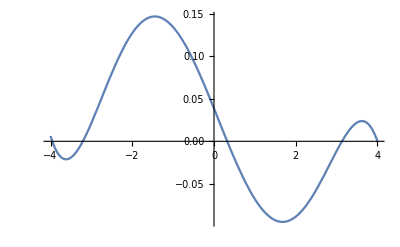

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.038648950043264366,b->-0.12002682647755564,c->-0.005685538619641221,d->0.01950434056105181,e->0.00021663351052674432,f->-0.0007532314471894658},{x,-4,4}]
```

```mathematica
F52[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.038648950043264366,b->-0.12002682647755564,c->-0.005685538619641221,d->0.01950434056105181,e->0.00021663351052674432,f->-0.0007532314471894658}
```

0.038649-0.120027 x-0.00568554 x^2+0.0195043 x^3+0.000216634 x^4-0.000753231 x^5

```mathematica
Solve[F52[x]==0,Reals]
```

{{x→-3.95726},{x→-3.20933},{x→0.322525},{x→3.13168},{x→4.}}

```mathematica
APN1 =-Integrate[F52[x],{x,-3.9572621702020925,-3.2093327748685505}]-Integrate[F52[x],{x,0.32252463475773246,3.1316758229953026}]
```

0.178799

```mathematica
AT1=Integrate[F52[x],{x,-4,-3.9572621702020925}]-Integrate[F52[x],{x,-3.9572621702020925,-3.2093327748685505}]+Integrate[F52[x],{x,-3.2093327748685505,0.32252463475773246}]-Integrate[F52[x],{x,0.32252463475773246,3.1316758229953026}]+Integrate[F52[x],{x,3.1316758229953026,4}]
```

0.512939

```mathematica
APN1/AT1
```

0.348577

```mathematica
(*Como el área de la parte total negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(-3.9572621702020925-3.2093327748685505)/2]
```

a-3.5833 b+12.84 c-46.0096 d+164.866 e-590.764 f

```mathematica
f[(0.32252463475773246+3.1316758229953026)/2]
```

a+1.7271 b+2.98288 c+5.15172 d+8.89754 e+15.367 f

```mathematica
Minimize[{F5[a,b,c,d,e,f],{a+4 b+16 c+64 d+256 e+1024 f>0,a-4 b+16 c-64 d+256 e-1024 f>0,a-3.1742771468162587 b+10.076035404799969 c-31.98412891596805 d+101.52648947878247 e-322.2732153489805 f>0,a+3.1737422670075865 b+10.072639977390455 c+31.96796323659443 d+101.4580761141244 e+322.0017844926694 f>0,
a-3.5832974725353215 b+12.840020776678022 c-46.00961399637137 d+164.8661335455233 e-590.7643996403444 f>0,
a+1.7271002288765176 b+2.9828752005853194 c+5.151724441640994 d+8.897544462266909 e+15.36695107722017 f>0}},{a,b,c,d,e,f}]
```

{379.996,{a→0.0663868,b→1.01778,c→-0.0103643,d→-0.164545,e→0.000413345,f→0.00630882}}

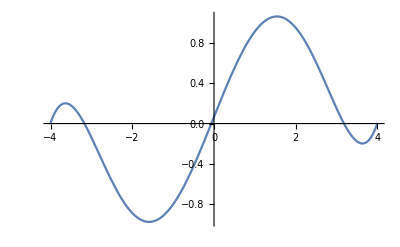

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.06638678508507787,b->1.0177817499264685,c->-0.010364251108672697,d->-0.16454456874650086,e->0.00041334462916230803,f->0.00630881842774529},{x,-4,4}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F53[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.06638678508507787,b->1.0177817499264685,c->-0.010364251108672697,d->-0.16454456874650086,e->0.00041334462916230803,f->0.00630881842774529}
```

0.0663868+1.01778 x-0.0103643 x^2-0.164545 x^3+0.000413345 x^4+0.00630882 x^5

```mathematica
Solve[F33[x]==0,Reals]
```

{{x→-4.00497},{x→-3.17044},{x→-0.0652285},{x→3.18082},{x→3.9943}}

```mathematica
f[(-3.1704352016489556-0.06522847754309209)/2]
```

a-1.61783 b+2.61738 c-4.23448 d+6.85068 e-11.0832 f

```mathematica
f[(3.180815834734834+3.9942951058503002)/2]
```

a+3.58756 b+12.8706 c+46.1738 d+165.651 e+594.283 f

```mathematica
Minimize[{F5[a,b,c,d,e,f],{a+4 b+16 c+64 d+256 e+1024 f>0,a-4 b+16 c-64 d+256 e-1024 f>0,a-3.1742771468162587 b+10.076035404799969 c-31.98412891596805 d+101.52648947878247 e-322.2732153489805 f>0,a+3.1737422670075865 b+10.072639977390455 c+31.96796323659443 d+101.4580761141244 e+322.0017844926694 f>0,
a-3.5832974725353215 b+12.840020776678022 c-46.00961399637137 d+164.8661335455233 e-590.7643996403444 f>0,
a+1.7271002288765176 b+2.9828752005853194 c+5.151724441640994 d+8.897544462266909 e+15.36695107722017 f>0,
a-1.6178318395960238 b+2.6173798612106545 c-4.234480475784019 d+6.8506773378711046 e-11.083243920006801 f>0,
a+3.587555470292567 b+12.870554252426123 c+46.173827313988596 d+165.65116676464416 e+594.2827494868454 f>0}},{a,b,c,d,e,f}]
```

{71.688,{a→0.0298084,b→-0.00346254,c→-0.00531268,d→0.000373307,e→0.000253151,f→-6.38981×10^-6}}

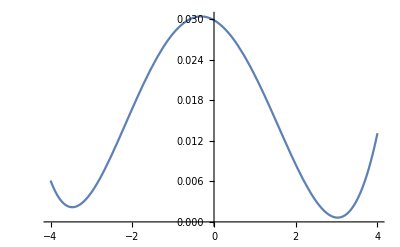

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.02980842184513065,b->-0.003462535971485079,c->-0.005312682756461376,d->0.00037330742632211614,e->0.00025315082321633814,f->-6.38981368105471*^-6},{x,-4,4}]
```

```mathematica
(*Como ya no hay parte negativa, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación*)
```

```mathematica
F54[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.{a->0.02980842184513065,b->-0.003462535971485079,c->-0.005312682756461376,d->0.00037330742632211614,e->0.00025315082321633814,f->-6.38981368105471*^-6}
```

0.0298084-0.00346254 x-0.00531268 x^2+0.000373307 x^3+0.000253151 x^4-6.38981×10^-6 x^5

```mathematica
Integrate[F54[x],{x,-4,4}]
```

0.115483

```mathematica
f5[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5)/0.11548348767477193/.{a->0.02980842184513065,b->-0.003462535971485079,c->-0.005312682756461376,d->0.00037330742632211614,e->0.00025315082321633814,f->-6.38981368105471*^-6}
```

8.65925 (0.0298084-0.00346254 x-0.00531268 x^2+0.000373307 x^3+0.000253151 x^4-6.38981×10^-6 x^5)

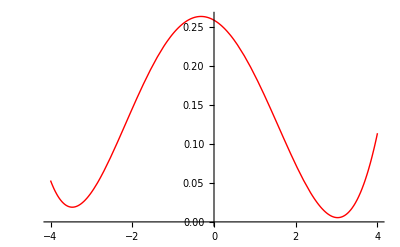

```mathematica
Plot[f5[x],{x,-4,4},PlotStyle->{Red,Thin}]
```

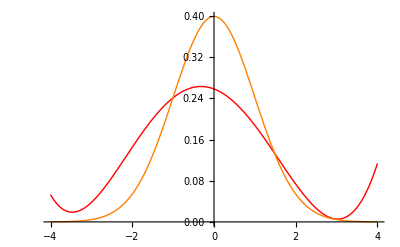

```mathematica
Plot[{f5[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Red,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL5= N[Integrate[F[x]*Log[F[x]/f5[x]],{x,-4,4}]]
```

0.153667

```mathematica
(*Verosimilitud*)
```

```mathematica
x5=Log[f5[datos]]
```

{-1.34248,-1.34705,-1.65725,-2.06435,-4.1926,-1.52667,-1.44896,-1.37475,-1.36845,-1.70228,-1.35873,-1.37951,-1.63899,-1.38359,9972,-1.50186,-1.34473,-1.73524,-1.33601,-1.71358,-1.38852,-1.39493,-1.72616,-1.3612,-1.45809,-1.46641,-1.41841,-1.64919,-1.33677}
 |  |  |  |

```mathematica
V5=Apply[Plus,x5]
```

-15674.5

```mathematica
(*BIC*)
```

```mathematica
BIC5 = -2*V5 + 6*Log[10000]
```

31404.3

### MOP DE GRADO 7

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13

```mathematica
(*Función de la suma de las diferencias al cuadrado entre los momentos poblacionales y los muestrales*)
```

```mathematica
F7[a_,b_,c_,d_,e_,f_,g_,h_]=((128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9-(Apply[Plus,datos])/10^4)^2+((128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9-(Apply[Plus,datos^2])/10^4)^2+((2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11-(Apply[Plus,datos^3])/10^4)^2+((2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11-(Apply[Plus,datos^4])/10^4)^2+((32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13-(Apply[Plus,datos^5])/10^4)^2+((32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13-(Apply[Plus,datos^6])/10^4)^2+((524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15-(Apply[Plus,datos^7])/10^4)^2+((524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15-(Apply[Plus,datos^8])/10^4)^2
```

(-0.992368+(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9)^2+(-2.9755+(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11)^2+(-14.7766+(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13)^2+(-100.868+(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15)^2+(0.0196627+(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9)^2+(0.0566338+(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11)^2+(0.355927+(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13)^2+(2.60393+(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15)^2

```mathematica
Minimize[F7[a,b,c,d,e,f,g,h],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h>0},{a,b,c,d,e,f,g,h}]
```

{0.00604643,{a→0.224882,b→-0.00252493,c→-0.0558423,d→0.000518764,e→0.00451611,f→-0.0000357874,g→-0.000119026,h→8.26731×10^-7}}

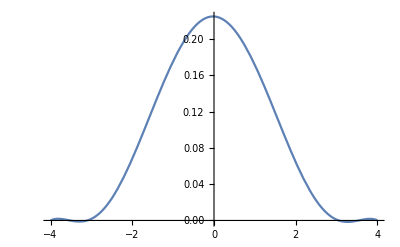

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{a->0.2248820383757399,b->-0.0025249344834354912,c->-0.05584231991811562,d->0.0005187642159087724,e->0.004516110248552674,f->-0.00003578744146269108,g->-0.00011902566966346229,h->8.267314571142728*^-7},{x,-4,4}]
```

```mathematica
F71[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7/.{a->0.2248820383757399,b->-0.0025249344834354912,c->-0.05584231991811562,d->0.0005187642159087724,e->0.004516110248552674,f->-0.00003578744146269108,g->-0.00011902566966346229,h->8.267314571142728*^-7}
```

0.224882-0.00252493 x-0.0558423 x^2+0.000518764 x^3+0.00451611 x^4-0.0000357874 x^5-0.000119026 x^6+8.26731×10^-7 x^7

```mathematica
Solve[F71[x]==0,Reals]
```

{{x→-4.},{x→-3.5257},{x→-3.10132},{x→3.05018},{x→3.5397},{x→4.},{x→144.009}}

```mathematica
APN=-Integrate[F71[x],{x,-3.525695380192145,-3.1013152062307228}]-Integrate[F71[x],{x,3.0501806531585007,3.5396953782699967}]
```

0.000844872

```mathematica
AT= Integrate[F71[x],{x,-4,-3.525695380192145}]-Integrate[F71[x],{x,-3.525695380192145,-3.1013152062307228}]+Integrate[F71[x],{x,-3.1013152062307228,3.0501806531585007}]-Integrate[F71[x],{x,3.0501806531585007,3.5396953782699967}]+Integrate[F71[x],{x,3.5396953782699967,4}]
```

0.710763

```mathematica
APN/AT
```

0.00118868

```mathematica
(*Como el área de la parte negativa es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
FindMinimum[F71[x],{x,-3}]
```

{-0.0012139,{x→-3.29202}}

```mathematica
FindMinimum[F71[x],{x,3}]
```

{-0.00158522,{x→3.26742}}

```mathematica
Integrate[F71[x]+0.0015852207994271439,{x,-4,4}]
```

0.721755

```mathematica
f7[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+0.0015852207994271439)/0.7217550180071504/.{a->0.2248820383757399,b->-0.0025249344834354912,c->-0.05584231991811562,d->0.0005187642159087724,e->0.004516110248552674,f->-0.00003578744146269108,g->-0.00011902566966346229,h->8.267314571142728*^-7}
```

1.38551 (0.226467-0.00252493 x-0.0558423 x^2+0.000518764 x^3+0.00451611 x^4-0.0000357874 x^5-0.000119026 x^6+8.26731×10^-7 x^7)

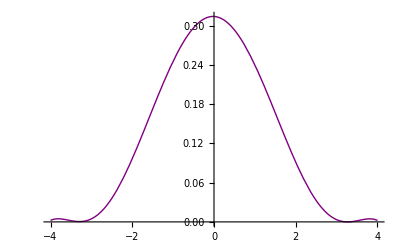

```mathematica
Plot[f7[x],{x,-4,4},PlotStyle->{Purple,Thin}]
```

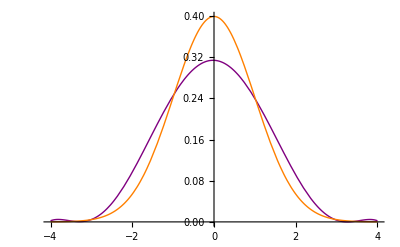

```mathematica
Plot[{f7[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Purple,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL7= N[Integrate[F[x]*Log[F[x]/f7[x]],{x,-4,4}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.28113}. NIntegrate obtained 0.0347379 and 0.0000158825 for the integral and error estimates.

0.0347379

```mathematica
(*Verosimilitud*)
```

```mathematica
x7=Log[f7[datos]]
```

{-1.2178,-1.15953,-1.84491,-1.82862,-3.98308,-1.60585,-1.45784,-1.16572,-1.16292,-1.92621,-1.1598,-1.16814,-1.39381,-1.32331,9972,-1.26339,-1.22538,-1.49005,-1.18428,-1.4682,-1.33412,-1.17722,-1.48088,-1.16042,-1.47567,-1.49178,-1.19357,-1.40389,-1.19195}
 |  |  |  |

```mathematica
V7=Apply[Plus,x7]
```

-14506.3

```mathematica
(*BIC*)
```

```mathematica
BIC7 = -2*V7 + 8*Log[10000]
```

29086.3

### MOP DE GRADO 9

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19

```mathematica
(*Función de la suma de las diferencias al cuadrado entre los momentos poblacionales y los muestrales*)
```

```mathematica
F9[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_]=((128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11-(Apply[Plus,datos])/10000)^2+((128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11-(Apply[Plus,datos^2])/10000)^2+((2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13-(Apply[Plus,datos^3])/10000)^2+((2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13-(Apply[Plus,datos^4])/10000)^2+((32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15-(Apply[Plus,datos^5])/10000)^2+((524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17-(Apply[Plus,datos^6])/10000)^2+((524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17-(Apply[Plus,datos^7])/10000)^2+((8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19-(Apply[Plus,datos^8])/10000)^2+((8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19-(Apply[Plus,datos^9])/10000)^2+((8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19-(Apply[Plus,datos^10])/10000)^2
```

(-0.992368+(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11)^2+(-2.9755+(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13)^2+(2.60393+(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17)^2+(-860.688+(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19)^2+(17.1996+(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19)^2+(0.0196627+(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11)^2+(0.0566338+(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13)^2+(0.355927+(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15)^2+(-14.7766+(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17)^2+(-100.868+(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19)^2

```mathematica
Minimize[F9[a,b,c,d,e,f,g,h,i,j],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j>0},{a,b,c,d,e,f,g,h,i,j}]
```

{385355.,{a→14.5552,b→7.50284,c→-12.2131,d→-5.11313,e→2.81421,f→1.0522,g→-0.241425,h→-0.0840134,i→0.00691403,j→0.00228912}}

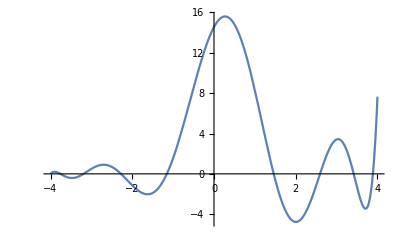

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->14.555170199809206,b->7.5028446700913705,c->-12.213144490282826,d->-5.113129439340336,e->2.8142116915948323,f->1.0521992627555676,g->-0.24142450293571222,h->-0.08401335829416771,i->0.0069140292401942164,j->0.0022891152585281776},{x,-4,4}]
```

```mathematica
F91[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->14.555170199809206,b->7.5028446700913705,c->-12.213144490282826,d->-5.113129439340336,e->2.8142116915948323,f->1.0521992627555676,g->-0.24142450293571222,h->-0.08401335829416771,i->0.0069140292401942164,j->0.0022891152585281776}
```

14.5552+7.50284 x-12.2131 x^2-5.11313 x^3+2.81421 x^4+1.0522 x^5-0.241425 x^6-0.0840134 x^7+0.00691403 x^8+0.00228912 x^9

```mathematica
Solve[F91[x]==0,Reals]
```

{{x→-4.},{x→-3.76054},{x→-3.19271},{x→-2.27636},{x→-1.154},{x→1.46097},{x→2.595},{x→3.41888},{x→3.88837}}

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9
```

a+b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7+i x^8+j x^9

```mathematica
f[(-3.7605428876172304-3.1927096823034096)/2]
```

a-3.47663 b+12.0869 c-42.0217 d+146.094 e-507.914 f+1765.83 g-6139.12 h+21343.4 i-74203.1 j

```mathematica
f[(-2.276360868024719-1.1540039913030862)/2]
```

a-1.71518 b+2.94185 c-5.04581 d+8.65449 e-14.844 f+25.4602 g-43.6689 h+74.9001 i-128.467 j

```mathematica
f[(1.4609727497202842+2.5950047005981123)/2]
```

a+2.02799 b+4.11274 c+8.34059 d+16.9146 e+34.3027 f+69.5654 g+141.078 h+286.104 i+580.216 j

```mathematica
f[(3.418876467709453+3.8883698397198874)/2]
```

a+3.65362 b+13.349 c+48.7721 d+178.195 e+651.057 f+2378.72 g+8690.93 h+31753.4 i+116015. j

```mathematica
Minimize[F9[a,b,c,d,e,f,g,h,i,j],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j>0,
a-3.47662628496032 b+12.086930325276995 c-42.02173967334199 d+146.09388468810064 e-507.9138395786127 f+1765.826605174124 g-6139.119190230608 h+21343.423143260046 i-74203.10591088829 j>0,
a-1.7151824296639027 b+2.9418507670277685 c-5.045810746299304 d+8.654485935461869 e-14.844022214277562 f+25.460206087469537 g-43.668898136849684 h+74.9001268071073 i-128.4673814791487 j>0,
a+2.027988725159198 b+4.11273826937283 c+8.340586839818853 d+16.91461607236382 e+34.30265068515039 f+69.56538883255944 g+141.07782421374614 h+286.1042368754685 i+580.2161666037266 j>0,
a+3.65362315371467 b+13.34896214935993 c+48.77207718696219 d+178.1947904650441 e+651.0566123144192 f+2378.715513130998 g+8690.930074875685 h+31753.38334888097 i+116014.89661224937 j>0},{a,b,c,d,e,f,g,h,i,j}]
```

{1.22815×10^10,{a→93056.6,b→34803.9,c→-47124.8,d→-16012.1,e→7772.29,f→2491.32,g→-519.773,h→-160.177,i→12.2136,j→3.65817}}

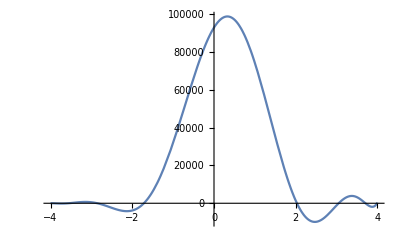

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->93056.5863777235,b->34803.886651120236,c->-47124.84895769066,d->-16012.125811219636,e->7772.29223618868,f->2491.324353935707,g->-519.7732921290225,h->-160.1774168509444,i->12.213562801135193,j->3.658165386119531},{x,-4,4}]
```

```mathematica
F92[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->93056.5863777235,b->34803.886651120236,c->-47124.84895769066,d->-16012.125811219636,e->7772.29223618868,f->2491.324353935707,g->-519.7732921290225,h->-160.1774168509444,i->12.213562801135193,j->3.658165386119531}
```

93056.6+34803.9 x-47124.8 x^2-16012.1 x^3+7772.29 x^4+2491.32 x^5-519.773 x^6-160.177 x^7+12.2136 x^8+3.65817 x^9

```mathematica
Solve[F92[x]==0,Reals]
```

{{x→-4.04108},{x→-3.93862},{x→-3.56413},{x→-2.85509},{x→-1.7157},{x→2.02933},{x→3.05106},{x→3.70543},{x→3.9901}}

```mathematica
APN=-Integrate[F92[x],{x,-3.9386216984229128,-3.5641329094673266}]-Integrate[F92[x],{x,-2.8550936186016127,-1.7157028584634926}]-Integrate[F92[x],{x,2.029333369918719,3.0510554974177846}]-Integrate[F92[x],{x,3.705428324764263,3.990100851906404}]
```

9694.42

```mathematica
AT=Integrate[F92[x],{x,-4,-3.9386216984229128}]-Integrate[F92[x],{x,-3.9386216984229128,-3.5641329094673266}]+Integrate[F92[x],{x,-3.5641329094673266,-2.8550936186016127}]-Integrate[F92[x],{x,-2.8550936186016127,-1.7157028584634926}]+Integrate[F92[x],{x,-1.7157028584634926,2.029333369918719}]-Integrate[F92[x],{x,2.029333369918719,3.0510554974177846}]+Integrate[F92[x],{x,3.0510554974177846,3.705428324764263}]-Integrate[F92[x],{x,3.705428324764263,3.990100851906404}]+Integrate[F92[x],{x,3.990100851906404,4}]
```

215071.

```mathematica
APN/AT
```

0.0450755

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(-3.9386216984229128-3.5641329094673266)/2]
```

a-3.75138 b+14.0728 c-52.7925 d+198.045 e-742.94 f+2787.05 g-10455.3 h+39221.7 i-147135. j

```mathematica
f[(-2.8550936186016127-1.7157028584634926)/2]
```

a-2.2854 b+5.22305 c-11.9367 d+27.2802 e-62.3461 f+142.486 g-325.637 h+744.209 i-1700.81 j

```mathematica
f[(2.029333369918719+3.0510554974177846)/2]
```

a+2.54019 b+6.45259 c+16.3908 d+41.6359 e+105.763 f+268.659 g+682.447 h+1733.55 i+4403.55 j

```mathematica
f[(3.705428324764263+3.990100851906404)/2]
```

a+3.84776 b+14.8053 c+56.9673 d+219.197 e+843.417 f+3245.27 g+12487. h+48047.2 i+184874. j

```mathematica
Minimize[F9[a,b,c,d,e,f,g,h,i,j],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j>0,
a-3.47662628496032 b+12.086930325276995 c-42.02173967334199 d+146.09388468810064 e-507.9138395786127 f+1765.826605174124 g-6139.119190230608 h+21343.423143260046 i-74203.10591088829 j>0,
a-1.7151824296639027 b+2.9418507670277685 c-5.045810746299304 d+8.654485935461869 e-14.844022214277562 f+25.460206087469537 g-43.668898136849684 h+74.9001268071073 i-128.4673814791487 j>0,
a+2.027988725159198 b+4.11273826937283 c+8.340586839818853 d+16.91461607236382 e+34.30265068515039 f+69.56538883255944 g+141.07782421374614 h+286.1042368754685 i+580.2161666037266 j>0,
a+3.65362315371467 b+13.34896214935993 c+48.77207718696219 d+178.1947904650441 e+651.0566123144192 f+2378.715513130998 g+8690.930074875685 h+31753.38334888097 i+116014.89661224937 j>0,
a-3.7513773039451195 b+14.072831676554554 c-52.792501353666694 d+198.04459139663726 e-742.9399853344299 f+2787.0481991768997 g-10455.269359393338 h+39221.66018146101 i-147135.24582778086 j>0,
a-2.2853982385325526 b+5.223045108687694 c-11.936738091170922 d+27.28020020738645 e-62.34612150077637 f+142.4857162572108 g-325.6366049502787 h+744.2093233550877 i-1700.8146766952202 j>0,
a+2.540194433668252 b+6.4525877608391715 c+16.390827512839554 d+41.635888811331476 e+105.76325299937447 f+268.65922655565805 g+682.4466718503004 h+1733.5472371095575 i+4403.5470422066755 j>0,
a+3.8477645883353335 b+14.805292327247379 c+56.96727953673528 d+219.19668089525013 e+843.4172266293835 f+3245.2709378165387 g+12487.038594084275 h+48047.18491549411 i+184874.25668703782 j>0},{a,b,c,d,e,f,g,h,i,j}]
```

{1.05348×10^12,{a→196208.,b→-9088.55,c→-68912.5,d→5290.13,e→8610.54,f→-936.949,g→-460.984,h→65.4403,i→9.015,j→-1.58334}}

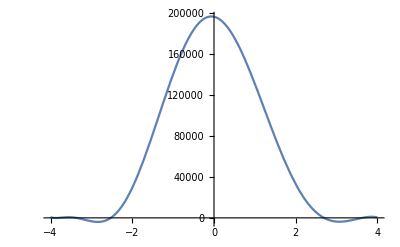

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->196207.87751154954,b->-9088.54987658777,c->-68912.46849889119,d->5290.129419532049,e->8610.544930729746,f->-936.9486449393236,g->-460.9844529257136,h->65.4402754487884,i->9.014998632449261,j->-1.5833418780082138},{x,-4,4}]
```

```mathematica
F93[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9/.{a->196207.87751154954,b->-9088.54987658777,c->-68912.46849889119,d->5290.129419532049,e->8610.544930729746,f->-936.9486449393236,g->-460.9844529257136,h->65.4402754487884,i->9.014998632449261,j->-1.5833418780082138}
```

196208.-9088.55 x-68912.5 x^2+5290.13 x^3+8610.54 x^4-936.949 x^5-460.984 x^6+65.4403 x^7+9.015 x^8-1.58334 x^9

```mathematica
Solve[F93[x]==0,Reals]
```

{{x→-3.9327},{x→-3.79697},{x→-3.36751},{x→-2.5256},{x→2.69171},{x→3.62737},{x→4.03644}}

```mathematica
APN1 =-  Integrate[F93[x],{x,-3.9326986645122637,-3.796968261673659}]-Integrate[F93[x],{x,-3.3675064487025006,-2.5255952844568754}]-Integrate[F93[x],{x,2.691708313750392,3.627367520541662}]
```

4258.76

```mathematica
AT1 = Integrate[F93[x],{x,-4,-3.9326986645122637}]-  Integrate[F93[x],{x,-3.9326986645122637,-3.796968261673659}]+  Integrate[F93[x],{x,-3.796968261673659,-3.3675064487025006}]-Integrate[F93[x],{x,-3.3675064487025006,-2.5255952844568754}]+Integrate[F93[x],{x,-2.5255952844568754,2.691708313750392}]-Integrate[F93[x],{x,2.691708313750392,3.627367520541662}]+Integrate[F93[x],{x,3.627367520541662,4}]
```

532022.

```mathematica
APN1/AT1
```

0.00800485

```mathematica
(*Como el área de la parte negativa ya es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
FindMinimum[F93[x],{x,-2}]
```

{-3936.88,{x→-2.84363}}

```mathematica
FindMinimum[F93[x],{x,3.1}]
```

{-3729.61,{x→3.07128}}

```mathematica
Integrate[F93[x]+3936.881666833906,{x,-4,4}]
```

555000.

```mathematica
f9[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+3936.881666833906)/554999.6090352319/.{a->196207.87751154954,b->-9088.54987658777,c->-68912.46849889119,d->5290.129419532049,e->8610.544930729746,f->-936.9486449393236,g->-460.9844529257136,h->65.4402754487884,i->9.014998632449261,j->-1.5833418780082138}
```

1.8018×10^-6 (200145.-9088.55 x-68912.5 x^2+5290.13 x^3+8610.54 x^4-936.949 x^5-460.984 x^6+65.4403 x^7+9.015 x^8-1.58334 x^9)

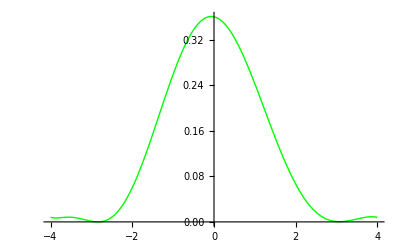

```mathematica
Plot[f9[x],{x,-4,4},PlotStyle->{Green,Thin}]
```

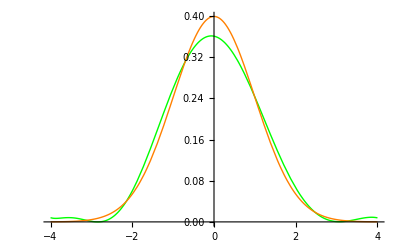

```mathematica
Plot[{f9[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Green,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL9= N[Integrate[F[x]*Log[F[x]/f9[x]],{x,-4,4}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.82825}. NIntegrate obtained 0.0214025 and 0.0000286602 for the integral and error estimates.

0.0214025

```mathematica
(*Verosimilitud*)
```

```mathematica
x9=Log[f9[datos]]
```

{-1.0886,-1.01845,-2.00735,-1.961,-4.87548,-1.64255,-1.42463,-1.03345,-1.02839,-2.13497,-1.02199,-1.03762,-1.36733,-1.23274,9972,-1.18185,-1.09864,-1.50109,-1.04549,-1.47088,-1.24789,-1.05257,-1.48843,-1.02341,-1.45054,-1.47402,-1.07819,-1.38143,-1.0551}
 |  |  |  |

```mathematica
V9=Apply[Plus,x9]
```

-14393.4

```mathematica
(*BIC*)
```

```mathematica
BIC9 = -2*V9 + 10*Log[10000]
```

28878.9

### MOP DE GRADO 11

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21

```mathematica
Integrate[x^11*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23

```mathematica
Integrate[x^12*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11),{x,-4,4}]
```

(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23

```mathematica
(*Funciónd de la suma de las diferencias al cuadrado entre los momentos poblacionales y los muestrales*)
```

```mathematica
F11[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_]=((128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13-(Apply[Plus,datos])/10000)^2+((128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13-(Apply[Plus,datos^2])/10000)^2+((2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15-(Apply[Plus,datos^3])/10000)^2+((2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15-(Apply[Plus,datos^4])/10000)^2+((32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17-(Apply[Plus,datos^5])/10000)^2+((32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17-(Apply[Plus,datos^6])/10000)^2+((524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19-(Apply[Plus,datos^7])/10000)^2+((524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19-(Apply[Plus,datos^8])/10000)^2+((8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21-(Apply[Plus,datos^9])/10000)^2+((8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21-(Apply[Plus,datos^10])/10000)^2+((134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23-(Apply[Plus,datos^11])/10000)^2+((134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23-(Apply[Plus,datos^12])/10000)^2
```

(-0.992368+(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13)^2+(-2.9755+(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15)^2+(-14.7766+(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17)^2+(-100.868+(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19)^2+(-860.688+(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21)^2+(-8625.74+(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23)^2+(0.0196627+(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13)^2+(0.0566338+(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15)^2+(0.355927+(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17)^2+(2.60393+(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19)^2+(17.1996+(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21)^2+(67.3493+(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23)^2

```mathematica
Minimize[F11[a,b,c,d,e,f,g,h,i,j,k,l],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l>0},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{7.07117×10^9,{a→20293.,b→2127.54,c→4950.75,d→2729.84,e→-5761.88,f→-1654.87,g→1130.46,h→289.437,i→-83.1169,j→-20.2558,k→2.09715,l→0.497079}}

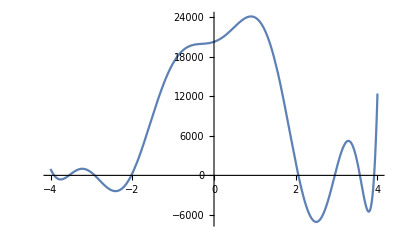

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->20293.01051226199,b->2127.5444117234915,c->4950.751717901743,d->2729.8420532053537,e->-5761.877801541665,f->-1654.8707568463085,g->1130.4609938870217,h->289.43731821171025,i->-83.11687459798732,j->-20.25582761125692,k->2.097151486909481,l->0.49707853934729196},{x,-4,4}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F11[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->20293.01051226199,b->2127.5444117234915,c->4950.751717901743,d->2729.8420532053537,e->-5761.877801541665,f->-1654.8707568463085,g->1130.4609938870217,h->289.43731821171025,i->-83.11687459798732,j->-20.25582761125692,k->2.097151486909481,l->0.49707853934729196}
```

20293.+2127.54 x+4950.75 x^2+2729.84 x^3-5761.88 x^4-1654.87 x^5+1130.46 x^6+289.437 x^7-83.1169 x^8-20.2558 x^9+2.09715 x^10+0.497079 x^11

```mathematica
Solve[F11[x]==0,Reals]
```

{{x→-4.50214},{x→-3.91093},{x→-3.54668},{x→-2.91947},{x→-2.02305},{x→2.06554},{x→2.95569},{x→3.57057},{x→3.91788}}

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11
```

a+b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7+i x^8+j x^9+k x^10+l x^11

```mathematica
f[(-3.9109311432193867-3.546675595332461)/2]
```

a-3.7288 b+13.904 c-51.8452 d+193.321 e-720.854 f+2687.92 g-10022.7 h+37372.8 i-139356. j+519631. k-1.9376×10^6 l

```mathematica
f[(-2.9194721077748467-2.023053934228448)/2]
```

a-2.47126 b+6.10714 c-15.0924 d+37.2972 e-92.1711 f+227.779 g-562.902 h+1391.08 i-3437.72 j+8495.51 k-20994.7 l

```mathematica
f[(2.0655359226775483+2.9556930896176508)/2]
```

a+2.51061 b+6.30319 c+15.8249 d+39.7301 e+99.7471 f+250.426 g+628.724 h+1578.48 i+3962.97 j+9949.48 k+24979.3 l

```mathematica
f[(3.5705666739544983+3.9178844750106894)/2]
```

a+3.74423 b+14.0192 c+52.4911 d+196.539 e+735.885 f+2755.32 g+10316.5 h+38627.5 i+144630. j+541527. k+2.0276×10^6 l

```mathematica
Minimize[F11[a,b,c,d,e,f,g,h,i,j,k,l],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l>0,
a-3.7288033692759237 b+13.90397456672348 c-51.845187210725264 d+193.3205087520934 e-720.8541643849416 f+2687.9234369151504 g-10022.737967924933 h+37372.819104168215 i-139355.89379496206 j+519630.72631111235 k-1.937600803048171*^6 l>0,
a-2.471263021001647 b+6.107140918970187 c-15.09235151709704 d+37.297170204160025 e-92.17111751354513 f+227.77907431562133 g-562.902003314181 h+1391.0789052380824 i-3437.7218578103275 j+8495.514903695745 k-20994.651825871664 l>0,
a+2.5106145061475997 b+6.303185198478756 c+15.824868194235602 d+39.73014364632168 e+99.7470749697831 f+250.42645336492956 g+628.7242865410875 h+1578.484314157355 i+3962.9656168499005 j+9949.47896502753 k+24979.306218208527 l>0,
a+3.744225574482594 b+14.019225152609511 c+52.49114135083018 d+196.53867387955918 e+735.8851291147397 f+2755.3199203128343 g+10316.539311516657 h+38627.45033033572 i+144629.88740389913 j+541526.9232522171 k+2.0275989553118243*^6 l>0},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{1.91455×10^14,{a→-1.95388×10^6,b→-219026.,c→2.27493×10^6,d→63107.9,e→-691195.,f→-1668.,g→86857.,h→-857.705,i→-4867.54,j→83.5474,k→100.859,l→-2.21927}}

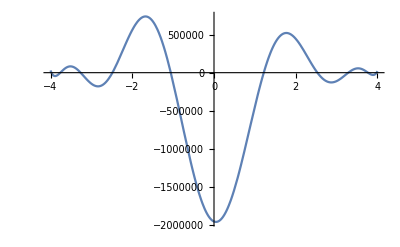

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->-1.9538841819088468*^6,b->-219025.78916096553,c->2.2749290410540146*^6,d->63107.93397260572,e->-691195.2647776844,f->-1668.000207472027,g->86857.03894661786,h->-857.7047867545997,i->-4867.5358408841985,j->83.54735179132302,k->100.85853053361835,l->-2.2192715481816383},{x,-4,4}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F112[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->-1.9538841819088468*^6,b->-219025.78916096553,c->2.2749290410540146*^6,d->63107.93397260572,e->-691195.2647776844,f->-1668.000207472027,g->86857.03894661786,h->-857.7047867545997,i->-4867.5358408841985,j->83.54735179132302,k->100.85853053361835,l->-2.2192715481816383}
```

-1.95388×10^6-219026. x+2.27493×10^6 x^2+63107.9 x^3-691195. x^4-1668. x^5+86857. x^6-857.705 x^7-4867.54 x^8+83.5474 x^9+100.859 x^10-2.21927 x^11

```mathematica
Solve[F112[x]==0,Reals]
```

{{x→-3.97799},{x→-3.75973},{x→-3.26362},{x→-2.48599},{x→-1.05744},{x→1.21778},{x→2.53022},{x→3.28619},{x→3.76725},{x→3.9785},{x→45.2115}}

```mathematica
f[(-3.977986963885731-3.759728845191454)/2]
```

a-3.86886 b+14.9681 c-57.9093 d+224.043 e-866.79 f+3353.49 g-12974.2 h+50195.2 i-194198. j+751325. k-2.90677×10^6 l

```mathematica
f[(-3.26362464954669-2.485986844399358)/2]
```

a-2.87481 b+8.26451 c-23.7589 d+68.3021 e-196.355 f+564.483 g-1622.78 h+4665.18 i-13411.5 j+38555.4 k-110839. l

```mathematica
f[(-1.0574386360321975)/2]
```

a-0.528719 b+0.279544 c-0.1478 d+0.0781449 e-0.0413167 f+0.021845 g-0.0115498 h+0.00610663 i-0.00322869 j+0.00170707 k-0.000902562 l

```mathematica
f[(1.2177798158420292)/2]
```

a+0.60889 b+0.370747 c+0.225744 d+0.137453 e+0.0836939 f+0.0509604 g+0.0310293 h+0.0188934 i+0.011504 j+0.00700467 k+0.00426507 l

```mathematica
f[(2.5302240640887756+3.2861949882693695)/2]
```

a+2.90821 b+8.45768 c+24.5967 d+71.5324 e+208.031 f+604.998 g+1759.46 h+5116.88 i+14881. j+43277. k+125859. l

```mathematica
f[(3.767254308734169+3.9785002842709867)/2]
```

a+3.87288 b+14.9992 c+58.09 d+224.975 e+871.302 f+3374.45 g+13068.8 h+50613.9 i+196021. j+759167. k+2.94016×10^6 l

```mathematica
Minimize[F11[a,b,c,d,e,f,g,h,i,j,k,l],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l>0,
a-3.7288033692759237 b+13.90397456672348 c-51.845187210725264 d+193.3205087520934 e-720.8541643849416 f+2687.9234369151504 g-10022.737967924933 h+37372.819104168215 i-139355.89379496206 j+519630.72631111235 k-1.937600803048171*^6 l>0,
a-2.471263021001647 b+6.107140918970187 c-15.09235151709704 d+37.297170204160025 e-92.17111751354513 f+227.77907431562133 g-562.902003314181 h+1391.0789052380824 i-3437.7218578103275 j+8495.514903695745 k-20994.651825871664 l>0,
a+2.5106145061475997 b+6.303185198478756 c+15.824868194235602 d+39.73014364632168 e+99.7470749697831 f+250.42645336492956 g+628.7242865410875 h+1578.484314157355 i+3962.9656168499005 j+9949.47896502753 k+24979.306218208527 l>0,
a+3.744225574482594 b+14.019225152609511 c+52.49114135083018 d+196.53867387955918 e+735.8851291147397 f+2755.3199203128343 g+10316.539311516657 h+38627.45033033572 i+144629.88740389913 j+541526.9232522171 k+2.0275989553118243*^6 l>0,
a-3.8688579045385927 b+14.96806148551075 c-57.90930299383793 d+224.04286463403028 e-866.790007794838 f+3353.487373232127 g-12974.166131699476 h+50195.205193422415 i-194198.11638250892 j+751324.9176129752 k-2.9067693463837663*^6 l>0,
a-2.874805746973024 b+8.264508082829128 c-23.758855332422186 d+68.30209385114799 e-196.35525193357108 f+564.4832067069661 g-1622.7795667109478 h+4665.176024451028 i-13411.47484573258 j+38555.38496189617 k-110839.24226521642 l>0,
a-0.5287193180160987 b+0.27954411724340855 c-0.1478003750243473 d+0.07814491348539655 e-0.041316725364425905 f+0.02184495085733771 g-0.011549847519386786 h+0.006106627503640112 i-0.0032286919291029514 j+0.001707071794839395 k-0.0009025618351720025 l>0,
a+0.6088899079210146 b+0.37074691996806164 c+0.22574405796135283 d+0.1374532786658043 e+0.08369391419026315 f+0.05096037970485862 g+0.031029260906111307 h+0.018893403815979256 i+0.011504002909826155 j+0.007004671272487131 k+0.004265073646121665 l>0,
a+2.9082095261790726 b+8.457682648158706 c+24.59671324677459 d+71.53239577696485 e+208.03119482898083 f+604.9983025440566 g+1759.4618267807941 h+5116.883645592338 i+14880.96976246154 j+43276.97802197338 k+125858.51974774535 l>0,
a+3.872877296502578 b+14.999178553765118 c+58.0899780870653 d+224.97535728772746 e+871.3019535121955 f+3374.4455541557263 g+13068.813574973772 h+50613.91138674063 i+196021.4682969011 j+759167.0941941681 k+2.940161003356428*^6 l>0},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{5.35881×10^16,{a→43881.4,b→-69802.6,c→556292.,d→608.639,e→-153157.,f→6258.84,g→14610.,h→-1125.97,i→-568.72,j→72.7355,k→7.34448,l→-1.61846}}

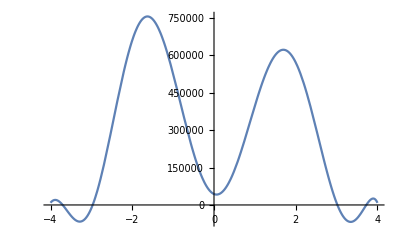

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->43881.38345220761,b->-69802.63985004803,c->556291.8032713374,d->608.6388447494355,e->-153157.18509097307,f->6258.842366345701,g->14610.032431608177,h->-1125.9667236351488,i->-568.719581880121,j->72.7355335305284,k->7.34447699197471,l->-1.6184628564944028},{x,-4,4}]
```

```mathematica
F113[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->43881.38345220761,b->-69802.63985004803,c->556291.8032713374,d->608.6388447494355,e->-153157.18509097307,f->6258.842366345701,g->14610.032431608177,h->-1125.9667236351488,i->-568.719581880121,j->72.7355335305284,k->7.34447699197471,l->-1.6184628564944028}
```

43881.4-69802.6 x+556292. x^2+608.639 x^3-153157. x^4+6258.84 x^5+14610. x^6-1125.97 x^7-568.72 x^8+72.7355 x^9+7.34448 x^10-1.61846 x^11

```mathematica
Solve[F113[x]==0,Reals]
```

{{x→-4.75852},{x→-4.03669},{x→-3.70384},{x→-2.96906},{x→3.01964},{x→3.727},{x→4.02056}}

```mathematica
APN2=-Integrate[F113[x],{x,-3.703844452242122,-2.969057287426028}]-Integrate[F113[x],{x,3.0196417674914184,3.7269996818194957}]
```

61973.1

```mathematica
AT2 = Integrate[F113[x],{x,-4,-3.703844452242122}]-Integrate[F113[x],{x,-3.703844452242122,-2.969057287426028}]+Integrate[F113[x],{x,-2.969057287426028,3.0196417674914184}]-Integrate[F113[x],{x,3.0196417674914184,3.7269996818194957}]+Integrate[F113[x],{x,3.7269996818194957,4}]
```

2.33917×10^6

```mathematica
APN2/AT2
```

0.0264937

```mathematica
f[(-3.703844452242122-2.969057287426028)/2]
```

a-3.33645 b+11.1319 c-37.1411 d+123.919 e-413.451 f+1379.46 g-4602.49 h+15356. i-51234.5 j+170941. k-570338. l

```mathematica
f[(3.0196417674914184+3.7269996818194957)/2]
```

a+3.37332 b+11.3793 c+38.386 d+129.488 e+436.806 f+1473.49 g+4970.54 h+16767.2 i+56561.2 j+190799. k+643627. l

```mathematica
Minimize[F11[a,b,c,d,e,f,g,h,i,j,k,l],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l>0,
a-3.7288033692759237 b+13.90397456672348 c-51.845187210725264 d+193.3205087520934 e-720.8541643849416 f+2687.9234369151504 g-10022.737967924933 h+37372.819104168215 i-139355.89379496206 j+519630.72631111235 k-1.937600803048171*^6 l>0,
a-2.471263021001647 b+6.107140918970187 c-15.09235151709704 d+37.297170204160025 e-92.17111751354513 f+227.77907431562133 g-562.902003314181 h+1391.0789052380824 i-3437.7218578103275 j+8495.514903695745 k-20994.651825871664 l>0,
a+2.5106145061475997 b+6.303185198478756 c+15.824868194235602 d+39.73014364632168 e+99.7470749697831 f+250.42645336492956 g+628.7242865410875 h+1578.484314157355 i+3962.9656168499005 j+9949.47896502753 k+24979.306218208527 l>0,
a+3.744225574482594 b+14.019225152609511 c+52.49114135083018 d+196.53867387955918 e+735.8851291147397 f+2755.3199203128343 g+10316.539311516657 h+38627.45033033572 i+144629.88740389913 j+541526.9232522171 k+2.0275989553118243*^6 l>0,
a-3.8688579045385927 b+14.96806148551075 c-57.90930299383793 d+224.04286463403028 e-866.790007794838 f+3353.487373232127 g-12974.166131699476 h+50195.205193422415 i-194198.11638250892 j+751324.9176129752 k-2.9067693463837663*^6 l>0,
a-2.874805746973024 b+8.264508082829128 c-23.758855332422186 d+68.30209385114799 e-196.35525193357108 f+564.4832067069661 g-1622.7795667109478 h+4665.176024451028 i-13411.47484573258 j+38555.38496189617 k-110839.24226521642 l>0,
a-0.5287193180160987 b+0.27954411724340855 c-0.1478003750243473 d+0.07814491348539655 e-0.041316725364425905 f+0.02184495085733771 g-0.011549847519386786 h+0.006106627503640112 i-0.0032286919291029514 j+0.001707071794839395 k-0.0009025618351720025 l>0,
a+0.6088899079210146 b+0.37074691996806164 c+0.22574405796135283 d+0.1374532786658043 e+0.08369391419026315 f+0.05096037970485862 g+0.031029260906111307 h+0.018893403815979256 i+0.011504002909826155 j+0.007004671272487131 k+0.004265073646121665 l>0,
a+2.9082095261790726 b+8.457682648158706 c+24.59671324677459 d+71.53239577696485 e+208.03119482898083 f+604.9983025440566 g+1759.4618267807941 h+5116.883645592338 i+14880.96976246154 j+43276.97802197338 k+125858.51974774535 l>0,
a+3.872877296502578 b+14.999178553765118 c+58.0899780870653 d+224.97535728772746 e+871.3019535121955 f+3374.4455541557263 g+13068.813574973772 h+50613.91138674063 i+196021.4682969011 j+759167.0941941681 k+2.940161003356428*^6 l>0,
a-3.336450869834075 b+11.131904406816556 c-37.14105214103287 d+123.91929572250186 e-413.4506420025673 f+1379.4577541429226 g-4602.493023709514 h+15355.991852360867 i-51234.51237297439 j+170941.43337233507 k-570337.694065811 l>0,
a+3.373320724655457 b+11.379292711390018 c+38.38600393525274 d+129.488302611494 e+436.80557479981 f+1473.4852981172387 g+4970.538493614006 h+16767.22051320584 i+56561.212452065374 j+190799.11017619242 k+643626.5926031698 l>0},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{2.58735×10^16,{a→20548.4,b→-177.862,c→-8275.5,d→51.6991,e→1316.23,f→-5.03857,g→-103.309,h→0.14086,i→4.00248,j→0.00468001,k→-0.0612561,l→-0.00023214}}

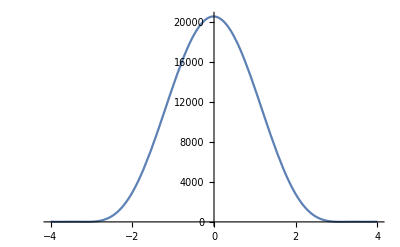

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->20548.419089978357,b->-177.86220416578934,c->-8275.49531215182,d->51.699113995245646,e->1316.2261593678263,f->-5.038567606284514,g->-103.30867957139095,h->0.1408601879209444,i->4.002477956757665,j->0.00468000824854046,k->-0.06125613241438023,l->-0.00023214012518379726},{x,-4,4}]
```

```mathematica
F114[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11/.{a->20548.419089978357,b->-177.86220416578934,c->-8275.49531215182,d->51.699113995245646,e->1316.2261593678263,f->-5.038567606284514,g->-103.30867957139095,h->0.1408601879209444,i->4.002477956757665,j->0.00468000824854046,k->-0.06125613241438023,l->-0.00023214012518379726}
```

20548.4-177.862 x-8275.5 x^2+51.6991 x^3+1316.23 x^4-5.03857 x^5-103.309 x^6+0.14086 x^7+4.00248 x^8+0.00468001 x^9-0.0612561 x^10-0.00023214 x^11

```mathematica
Solve[F114[x]==0,Reals]
```

{{x→-263.704},{x→-4.22463},{x→4.1499}}

```mathematica
(*Como ya no hay parte negativa, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación*)
```

```mathematica
Integrate[F114[x],{x,-4,4}]
```

53270.4

```mathematica
f11[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11)/53270.36935865338/.{a->20548.419089978357,b->-177.86220416578934,c->-8275.49531215182,d->51.699113995245646,e->1316.2261593678263,f->-5.038567606284514,g->-103.30867957139095,h->0.1408601879209444,i->4.002477956757665,j->0.00468000824854046,k->-0.06125613241438023,l->-0.00023214012518379726}
```

0.0000187722 (20548.4-177.862 x-8275.5 x^2+51.6991 x^3+1316.23 x^4-5.03857 x^5-103.309 x^6+0.14086 x^7+4.00248 x^8+0.00468001 x^9-0.0612561 x^10-0.00023214 x^11)

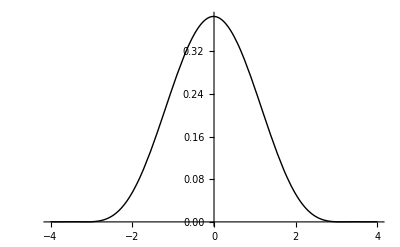

```mathematica
Plot[f11[x],{x,-4,4},PlotStyle->{Black,Thin}]
```

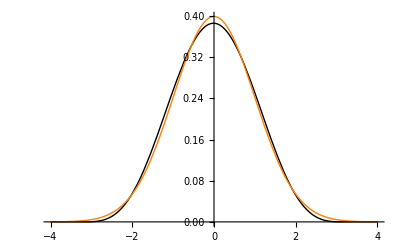

```mathematica
Plot[{f11[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Black,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL11= N[Integrate[F[x]*Log[F[x]/f11[x]],{x,-4,4}]]
```

0.0108559

```mathematica
(*Verosimilitud*)
```

```mathematica
x11=Log[f11[datos]]
```

{-1.0533,-0.953993,-2.08711,-2.03219,-5.58958,-1.69425,-1.45061,-0.962074,-0.957871,-2.22064,-0.953421,-0.965754,-1.32714,-1.22854,9972,-1.11702,-1.06597,-1.48279,-0.997007,-1.44742,-1.24642,-0.979833,-1.46795,-0.954257,-1.47999,-1.50651,-1.00556,-1.34342,-1.00994}
 |  |  |  |

```mathematica
V11=Apply[Plus,x11]
```

-14259.6

```mathematica
(*BIC*)
```

```mathematica
BIC11 = -2*V11 + 12*Log[10000]
```

28629.8

### MOP DE GRADO 13

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23

```mathematica
Integrate[x^11*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25

```mathematica
Integrate[x^12*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25

```mathematica
Integrate[x^13*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27

```mathematica
Integrate[x^14*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13),{x,-4,4}]
```

(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27

```mathematica
F13[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_]=((128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15-(Apply[Plus,datos])/10000)^2+((128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15-(Apply[Plus,datos^2])/10000)^2+((2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17-(Apply[Plus,datos^3])/10000)^2+((2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17-(Apply[Plus,datos^4])/10000)^2+((32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19-(Apply[Plus,datos^5])/10000)^2+((32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19-(Apply[Plus,datos^6])/10000)^2+((524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21-(Apply[Plus,datos^7])/10000)^2+((524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21-(Apply[Plus,datos^8])/10000)^2+((8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23-(Apply[Plus,datos^9])/10000)^2+((8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23-(Apply[Plus,datos^10])/10000)^2+((134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25-(Apply[Plus,datos^11])/10000)^2+((134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25-(Apply[Plus,datos^12])/10000)^2+((2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27-(Apply[Plus,datos^13])/10000)^2+((2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27-(Apply[Plus,datos^14])/10000)^2
```

(-0.992368+(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15)^2+(-2.9755+(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17)^2+(-14.7766+(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19)^2+(-100.868+(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21)^2+(-860.688+(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23)^2+(-8625.74+(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25)^2+(-96986.7+(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27)^2+(0.0196627+(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15)^2+(0.0566338+(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17)^2+(0.355927+(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19)^2+(2.60393+(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21)^2+(17.1996+(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23)^2+(67.3493+(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25)^2+(-763.198+(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27)^2

```mathematica
Minimize[F13[a,b,c,d,e,f,g,h,i,j,k,l,m,n],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l+4^12m-4^13n>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l+4^12m+4^13n>0},{a,b,c,d,e,f,g,h,i,j,k,l,m,n}]
```

{1.79629×10^13,{a→8.50253,b→-0.703411,c→26.8138,d→-1.6983,e→-3.08475,f→-2.25234,g→-563.651,h→10.3154,i→143.084,j→-2.50711,k→-11.7727,l→0.203096,m→0.315488,n→-0.00539885}}

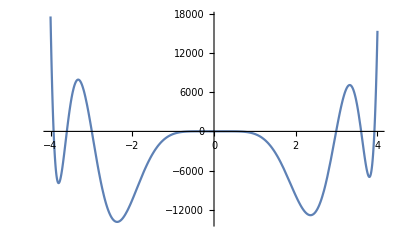

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->8.50253349959675,b->-0.7034108128412495,c->26.813808610729556,d->-1.6983045989772299,e->-3.0847463402652266,f->-2.2523368540739357,g->-563.6510939637885,h->10.31538033162874,i->143.08385965207543,j->-2.507108631230701,k->-11.772741298987814,l->0.20309597885009378,m->0.3154876746769094,n->-0.005398847450870817},{x,-4,4}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13
```

a+b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7+i x^8+j x^9+k x^10+l x^11+m x^12+n x^13

```mathematica
F131[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->8.50253349959675,b->-0.7034108128412495,c->26.813808610729556,d->-1.6983045989772299,e->-3.0847463402652266,f->-2.2523368540739357,g->-563.6510939637885,h->10.31538033162874,i->143.08385965207543,j->-2.507108631230701,k->-11.772741298987814,l->0.20309597885009378,m->0.3154876746769094,n->-0.005398847450870817}
```

8.50253-0.703411 x+26.8138 x^2-1.6983 x^3-3.08475 x^4-2.25234 x^5-563.651 x^6+10.3154 x^7+143.084 x^8-2.50711 x^9-11.7727 x^10+0.203096 x^11+0.315488 x^12-0.00539885 x^13

```mathematica
Solve[F131[x]==0,Reals]
```

{{x→-3.9249},{x→-3.60099},{x→-2.98968},{x→-0.568508},{x→0.559441},{x→2.98936},{x→3.60086},{x→3.92488},{x→58.4413}}

```mathematica
f[(-3.9249027263140537-3.6009946929796257)/2]
```

a-3.76295 b+14.1598 c-53.2825 d+200.499 e-754.469 f+2839.03 g-10683.1 h+40200. i-151271. j+569224. k-2.14196×10^6 l+8.06008×10^6 m-3.03297×10^7 n

```mathematica
f[(-2.989678962100732-0.5685076466838086)/2]
```

a-1.77909 b+3.16517 c-5.63114 d+10.0183 e-17.8235 f+31.7097 g-56.4145 h+100.367 i-178.562 j+317.678 k-565.179 l+1005.51 m-1788.89 n

```mathematica
f[(0.5594410379139306+2.9893585095467685)/2]
```

a+1.7744 b+3.14849 c+5.58669 d+9.91302 e+17.5897 f+31.2111 g+55.3809 h+98.2679 i+174.367 j+309.396 k+548.992 l+974.132 m+1728.5 n

```mathematica
f[(3.6008596538727065+3.924876392331112)/2]
```

a+3.76287 b+14.1592 c+53.2791 d+200.482 e+754.388 f+2838.66 g+10681.5 h+40193.1 i+151241. j+569102. k+2.14145×10^6 l+8.05801×10^6 m+3.03212×10^7 n

```mathematica
Minimize[F13[a,b,c,d,e,f,g,h,i,j,k,l,m,n],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l+4^12m-4^13n>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l+4^12m+4^13n>0,
a-3.7629487096468397 b+14.159782991432817 c-53.282537136491385 d+200.4994543644701 e-754.4691630856781 f+2839.0287637015836 g-10683.119623021137 h+40200.03120045023 i-151270.65553349687 j+569223.7180472036 k-2.1419596553261015*^6 l+8.060084321124942*^6 m-3.0329683895821825*^7 n>0,
a-1.7790933043922703 b+3.1651729857334074 c-5.631138066161596 d+10.018320029616532 e-17.823526085949744 f+31.709715920174162 g-56.41454327776283 h+100.3667362158158 i-178.5617883852631 j+317.67808213653103 k-565.17894888128 l+1005.5060837381467 m-1788.8891411042302 n>0,
a+1.7743997737303496 b+3.148494557014316 c+5.58668802955744 d+9.913017975548774 e+17.589656852798633 f+31.211083139600387 g+55.38093886078606 h+98.26792538355312 i+174.36658456552755 j+309.39602819920594 k+548.9922424297399 l+974.1317107470476 m+1728.4990871331197 n>0,
a+3.762868023101909 b+14.159175759282869 c+53.2791096980852 d+200.4822581822636 e+754.3882785133007 f+2838.6635302205964 g+10681.516226212661 h+40193.1358458598 i+151241.4656225769 j+569101.6747582614 k+2.141454493841605*^6 l+8.058010637804459*^6 m+3.032123055880942*^7 n>0},{a,b,c,d,e,f,g,h,i,j,k,l,m,n}]
```

{3.93382×10^20,{a→63.048,b→-77.7702,c→121300.,d→-18576.5,e→405253.,f→-62378.9,g→-244848.,h→37399.,i→40901.9,j→-6218.86,k→-2676.95,l→405.465,m→61.0199,n→-9.21031}}

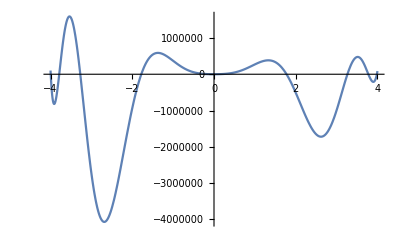

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->63.04803141924276,b->-77.77018721202603,c->121300.41044549775,d->-18576.492923398248,e->405253.2560907314,f->-62378.878052628395,g->-244847.84066756433,h->37399.01551892635,i->40901.939422947755,j->-6218.858418636039,k->-2676.9519916762997,l->405.4646828237906,m->61.019888031080114,n->-9.210309313355497},{x,-4,4}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F132[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->63.04803141924276,b->-77.77018721202603,c->121300.41044549775,d->-18576.492923398248,e->405253.2560907314,f->-62378.878052628395,g->-244847.84066756433,h->37399.01551892635,i->40901.939422947755,j->-6218.858418636039,k->-2676.9519916762997,l->405.4646828237906,m->61.019888031080114,n->-9.210309313355497}
```

63.048-77.7702 x+121300. x^2-18576.5 x^3+405253. x^4-62378.9 x^5-244848. x^6+37399. x^7+40901.9 x^8-6218.86 x^9-2676.95 x^10+405.465 x^11+61.0199 x^12-9.21031 x^13

```mathematica
Solve[F132[x]==0,Reals]
```

{{x→-3.99554},{x→-3.78705},{x→-3.27204},{x→-1.77925},{x→1.77452},{x→3.26503},{x→3.77693},{x→3.98564},{x→6.65701}}

```mathematica
f[(-3.99554299503042-3.7870535371410723)/2]
```

a-3.8913 b+15.1422 c-58.9228 d+229.286 e-892.221 f+3471.9 g-13510.2 h+52572.2 i-204574. j+796059. k-3.0977×10^6 l+1.20541×10^7 m-4.6906×10^7 n

```mathematica
f[(-3.2720438783856265-1.7792543644692793)/2]
```

a-2.52565 b+6.3789 c-16.1109 d+40.6904 e-102.77 f+259.56 g-655.558 h+1655.71 i-4181.74 j+10561.6 k-26674.9 l+67371.5 m-170157. n

```mathematica
f[(1.774515160751024+3.2650328193981677)/2]
```

a+2.51977 b+6.34926 c+15.9987 d+40.3131 e+101.58 f+255.958 g+644.958 h+1625.15 i+4095. j+10318.5 k+26000.2 l+65514.7 m+165082. n

```mathematica
f[(3.7769325331128503+3.9856360838138976)/2]
```

a+3.88128 b+15.0644 c+58.4691 d+226.935 e+880.8 f+3418.64 g+13268.7 h+51499.6 i+199884. j+775809. k+3.01113×10^6 l+1.16871×10^7 m+4.53608×10^7 n

```mathematica
Minimize[F13[a,b,c,d,e,f,g,h,i,j,k,l,m,n],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l+4^12m-4^13n>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l+4^12m+4^13n>0,
a-3.7629487096468397 b+14.159782991432817 c-53.282537136491385 d+200.4994543644701 e-754.4691630856781 f+2839.0287637015836 g-10683.119623021137 h+40200.03120045023 i-151270.65553349687 j+569223.7180472036 k-2.1419596553261015*^6 l+8.060084321124942*^6 m-3.0329683895821825*^7 n>0,
a-1.7790933043922703 b+3.1651729857334074 c-5.631138066161596 d+10.018320029616532 e-17.823526085949744 f+31.709715920174162 g-56.41454327776283 h+100.3667362158158 i-178.5617883852631 j+317.67808213653103 k-565.17894888128 l+1005.5060837381467 m-1788.8891411042302 n>0,
a+1.7743997737303496 b+3.148494557014316 c+5.58668802955744 d+9.913017975548774 e+17.589656852798633 f+31.211083139600387 g+55.38093886078606 h+98.26792538355312 i+174.36658456552755 j+309.39602819920594 k+548.9922424297399 l+974.1317107470476 m+1728.4990871331197 n>0,
a+3.762868023101909 b+14.159175759282869 c+53.2791096980852 d+200.4822581822636 e+754.3882785133007 f+2838.6635302205964 g+10681.516226212661 h+40193.1358458598 i+151241.4656225769 j+569101.6747582614 k+2.141454493841605*^6 l+8.058010637804459*^6 m+3.032123055880942*^7 n>0,
a-3.8912982660857462 b+15.142202195641936 c-58.92282514862124 d+229.28628733370346 e-892.2213323388785 f+3471.899323494992 g-13510.195817540338 h+52572.20155927362 i-204574.1167719118 j+796058.9058805634 k-3.097702640155153*^6 l+1.2054084912484985*^7 m-4.6906039719203174*^7 n>0,
a-2.525649121427453 b+6.378903484567266 c-16.110871981467835 d+40.690409665424404 e-102.7696974220023 f+259.5601960032453 g-655.557980993134 h+1655.709438740064 i-4181.741089292984 j+10561.610708209906 k-26674.92280604913 l+67371.49534924312 m-170156.75803806965 n>0,
a+2.519773990074596 b+6.34926096105645 c+15.998702625866073 d+40.31311475159547 e+101.57993800996277 f+255.958485710894 g+644.9575348331908 h+1625.1472209753044 i+4095.0036974555837 j+10318.48380610788 k+26000.24711163656 l+65514.74640741393 m+165082.3539637347 n>0,
a+3.881284308463374 b+15.06436788312401 c+58.46909468168884 d+226.93517971809817 e+880.7999520781701 f+3418.635032896294 g+13268.694509543557 h+51499.575793685515 i+199884.4954205518 j+775808.5555809068 k+3.0111335731478087*^6 l+1.1687065488145845*^7 m+4.536082389112431*^7 n>0},{a,b,c,d,e,f,g,h,i,j,k,l,m,n}]
```

{1.19667×10^23,{a→6.38191×10^8,b→2.40669×10^7,c→-8.72922×10^8,d→-5.2342×10^7,e→3.8507×10^8,f→2.71003×10^7,g→-7.32982×10^7,h→-5.55043×10^6,i→6.81582×10^6,j→538395.,k→-306431.,l→-24897.4,m→5341.44,n→443.033}}

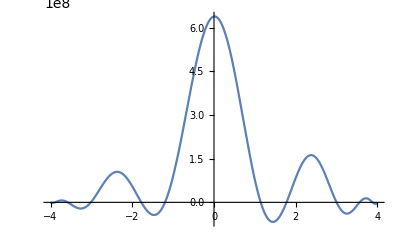

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->6.381906162915721*^8,b->2.4066900952438504*^7,c->-8.729224738511845*^8,d->-5.234200863233403*^7,e->3.850700773484922*^8,f->2.710025790311888*^7,g->-7.329815759890711*^7,h->-5.550428473957796*^6,i->6.815815017776689*^6,j->538394.6844942301,k->-306430.59852170496,l->-24897.390725498724,m->5341.436905533159,n->443.0332378652588},{x,-4,4}]
```

```mathematica
F133[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->6.381906162915721*^8,b->2.4066900952438504*^7,c->-8.729224738511845*^8,d->-5.234200863233403*^7,e->3.850700773484922*^8,f->2.710025790311888*^7,g->-7.329815759890711*^7,h->-5.550428473957796*^6,i->6.815815017776689*^6,j->538394.6844942301,k->-306430.59852170496,l->-24897.390725498724,m->5341.436905533159,n->443.0332378652588}
```

6.38191×10^8+2.40669×10^7 x-8.72922×10^8 x^2-5.2342×10^7 x^3+3.8507×10^8 x^4+2.71003×10^7 x^5-7.32982×10^7 x^6-5.55043×10^6 x^7+6.81582×10^6 x^8+538395. x^9-306431. x^10-24897.4 x^11+5341.44 x^12+443.033 x^13

```mathematica
Solve[F133[x]==0,Reals]
```

{{x→-11.9545},{x→-3.9995},{x→-3.8915},{x→-3.57909},{x→-3.01424},{x→-1.77905},{x→-1.19902},{x→1.14307},{x→1.77435},{x→2.99865},{x→3.56311},{x→3.88135},{x→3.99987}}

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13
```

a+b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7+i x^8+j x^9+k x^10+l x^11+m x^12+n x^13

```mathematica
APN = -Integrate[F133[x],{x,-3.9995015547102764,-3.891496394531871}]-Integrate[F133[x],{x,-3.5790894892511615,-3.0142351020558116}]-Integrate[F133[x],{x,-1.7790512490656372,-1.1990210174349167}]-Integrate[F133[x],{x,1.1430715831172453,1.7743453949459467}]-Integrate[F133[x],{x,2.99864920184205,3.5631058680629666}]-Integrate[F133[x],{x,3.8813516498717098,3.9998692723523197}]
```

6.62284×10^7

```mathematica
AT= Integrate[F133[x],{x,-4,-3.9995015547102764}]-Integrate[F133[x],{x,-3.9995015547102764,-3.891496394531871}]+Integrate[F133[x],{x,-3.891496394531871,-3.5790894892511615}]-Integrate[F133[x],{x,-3.5790894892511615,-3.0142351020558116}]+Integrate[F133[x],{x,-3.0142351020558116,-1.7790512490656372}]-Integrate[F133[x],{x,-1.7790512490656372,-1.1990210174349167}]+Integrate[F133[x],{x,-1.1990210174349167,1.1430715831172453}]-Integrate[F133[x],{x,1.1430715831172453,1.7743453949459467}]+Integrate[F133[x],{x,1.7743453949459467,2.99864920184205}]-Integrate[F133[x],{x,2.99864920184205,3.5631058680629666}]+Integrate[F133[x],{x,3.5631058680629666,3.8813516498717098}]-Integrate[F133[x],{x,3.8813516498717098,3.9998692723523197}]+Integrate[F133[x],{x,3.9998692723523197,4}]
```

1.112×10^9

```mathematica
APN/AT
```

0.0595579

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
f[(-3.9995015547102764-3.891496394531871)/2]
```

a-3.9455 b+15.567 c-61.4194 d+242.33 e-956.114 f+3772.35 g-14883.8 h+58724. i-231695. j+914154. k-3.60679×10^6 l+1.42306×10^7 m-5.61468×10^7 n

```mathematica
f[(-3.5790894892511615-3.0142351020558116)/2]
```

a-3.29666 b+10.868 c-35.8281 d+118.113 e-389.379 f+1283.65 g-4231.76 h+13950.7 i-45990.7 j+151616. k-499826. l+1.64776×10^6 m-5.4321×10^6 n

```mathematica
f[(-1.7790512490656372-1.1990210174349167)/2]
```

a-1.48904 b+2.21723 c-3.30153 d+4.9161 e-7.32025 f+10.9001 g-16.2307 h+24.1681 i-35.9871 j+53.5861 k-79.7917 l+118.813 m-176.916 n

```mathematica
f[(1.1430715831172453+1.7743453949459467)/2]
```

a+1.45871 b+2.12783 c+3.10388 d+4.52766 e+6.60454 f+9.6341 g+14.0533 h+20.4997 i+29.9031 j+43.6199 k+63.6288 l+92.8158 m+135.391 n

```mathematica
f[(2.99864920184205+3.5631058680629666)/2]
```

a+3.28088 b+10.7642 c+35.3159 d+115.867 e+380.146 f+1247.21 g+4091.95 h+13425.2 i+44046.4 j+144511. k+474122. l+1.55554×10^6 m+5.10353×10^6 n

```mathematica
f[(3.8813516498717098+3.9998692723523197)/2]
```

a+3.94061 b+15.5284 c+61.1914 d+241.132 e+950.205 f+3744.39 g+14755.2 h+58144.4 i+229125. j+902890. k+3.55794×10^6 l+1.40205×10^7 m+5.52491×10^7 n

```mathematica
Minimize[F13[a,b,c,d,e,f,g,h,i,j,k,l,m,n],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l+4^12m-4^13n>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l+4^12m+4^13n>0,
a-3.7629487096468397 b+14.159782991432817 c-53.282537136491385 d+200.4994543644701 e-754.4691630856781 f+2839.0287637015836 g-10683.119623021137 h+40200.03120045023 i-151270.65553349687 j+569223.7180472036 k-2.1419596553261015*^6 l+8.060084321124942*^6 m-3.0329683895821825*^7 n>0,
a-1.7790933043922703 b+3.1651729857334074 c-5.631138066161596 d+10.018320029616532 e-17.823526085949744 f+31.709715920174162 g-56.41454327776283 h+100.3667362158158 i-178.5617883852631 j+317.67808213653103 k-565.17894888128 l+1005.5060837381467 m-1788.8891411042302 n>0,
a+1.7743997737303496 b+3.148494557014316 c+5.58668802955744 d+9.913017975548774 e+17.589656852798633 f+31.211083139600387 g+55.38093886078606 h+98.26792538355312 i+174.36658456552755 j+309.39602819920594 k+548.9922424297399 l+974.1317107470476 m+1728.4990871331197 n>0,
a+3.762868023101909 b+14.159175759282869 c+53.2791096980852 d+200.4822581822636 e+754.3882785133007 f+2838.6635302205964 g+10681.516226212661 h+40193.1358458598 i+151241.4656225769 j+569101.6747582614 k+2.141454493841605*^6 l+8.058010637804459*^6 m+3.032123055880942*^7 n>0,
a-3.8912982660857462 b+15.142202195641936 c-58.92282514862124 d+229.28628733370346 e-892.2213323388785 f+3471.899323494992 g-13510.195817540338 h+52572.20155927362 i-204574.1167719118 j+796058.9058805634 k-3.097702640155153*^6 l+1.2054084912484985*^7 m-4.6906039719203174*^7 n>0,
a-2.525649121427453 b+6.378903484567266 c-16.110871981467835 d+40.690409665424404 e-102.7696974220023 f+259.5601960032453 g-655.557980993134 h+1655.709438740064 i-4181.741089292984 j+10561.610708209906 k-26674.92280604913 l+67371.49534924312 m-170156.75803806965 n>0,
a+2.519773990074596 b+6.34926096105645 c+15.998702625866073 d+40.31311475159547 e+101.57993800996277 f+255.958485710894 g+644.9575348331908 h+1625.1472209753044 i+4095.0036974555837 j+10318.48380610788 k+26000.24711163656 l+65514.74640741393 m+165082.3539637347 n>0,
a+3.881284308463374 b+15.06436788312401 c+58.46909468168884 d+226.93517971809817 e+880.7999520781701 f+3418.635032896294 g+13268.694509543557 h+51499.575793685515 i+199884.4954205518 j+775808.5555809068 k+3.0111335731478087*^6 l+1.1687065488145845*^7 m+4.536082389112431*^7 n>0,
a-3.9454989746210734 b+15.566962158735942 c-61.419433235257706 d+242.33031085151677 e-956.1139929842653 f+3772.346778940279 g-14883.79034822398 h+58723.97955739275 i-231695.40112936197 j+914153.9675803158 k-3.606793541733922*^6 l+1.4230600220581098*^7 m-5.614681857854514*^7 n>0,
a-3.2966622956534866 b+10.867982291583315 c-35.82806745049249 d+118.11303909016853 e-389.378802593605 f+1283.6504172370394 g-4231.761931305214 h+13950.690003115678 i-45990.71373162148 j+151615.8519092296 k-499826.26241253986 l+1.6477583936728253*^6 m-5.4321029687677575*^6 n>0,
a-1.489036133250277 b+2.217228606124937 c-3.301533510196178 d+4.916102691818731 e-7.320254542887041 f+10.900123518948295 g-16.230677776605173 h+24.16806567650737 i-35.98712306308528 j+53.586126572658365 k-79.79167870761114 l+118.81269272832975 m-176.91639256124543 n>0,
a+1.458708489031596 b+2.127830455972842 c+3.1038843493475565 d+4.527662449365593 e+6.604539650359179 f+9.634098054124705 g+14.053340615714488 h+20.499727255395243 i+29.90312617027742 j+43.619943993166544 k+63.62878259391481 l+92.81584531648942 m+135.39126147980662 n>0,
a+3.2808775349525083 b+10.764157399356048 c+35.315882194240075 d+115.86708451811155 e+380.1457146359158 f+1247.2115351574432 g+4091.948307031686 h+13425.181274727207 i+44046.37564691757 j+144510.76435605114 k+474122.12033458386 l+1.5555366134297862*^6 m+5.10352512979789*^6 n>0,
a+3.9406104611120147 b+15.528410806225445 c+61.191418067456844 d+241.13154216689915 e+950.2054775669557 f+3744.3896451062838 g+14755.181005985327 h+58144.42062778706 i+229124.51218115492 j+902890.4495982463 k+3.5579395509249796*^6 l+1.4020453814379161*^7 m+5.5249146970480375*^7 n>0},{a,b,c,d,e,f,g,h,i,j,k,l,m,n}]
```

{3.82676×10^21,{a→1.35689×10^9,b→-2.36864×10^8,c→-7.03706×10^8,d→1.16531×10^8,e→1.47661×10^8,f→-2.29773×10^7,g→-1.61381×10^7,h→2.33973×10^6,i→972727.,j→-130327.,k→-30747.4,l→3775.32,m→399.066,n→-44.5013}}

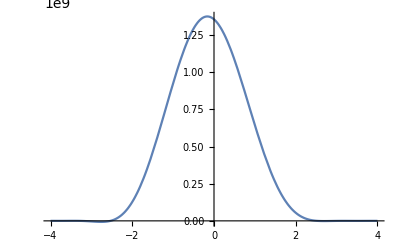

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->1.3568862505537734*^9,b->-2.368640788136678*^8,c->-7.037058922966869*^8,d->1.1653072288415925*^8,e->1.4766086494151035*^8,f->-2.2977312750058938*^7,g->-1.6138079970216721*^7,h->2.339733135292994*^6,i->972726.6767468101,j->-130326.61725571452,k->-30747.396074398228,l->3775.318565043793,m->399.0658437930184,n->-44.501331881484575},{x,-4,4}]
```

```mathematica
F134[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13/.{a->1.3568862505537734*^9,b->-2.368640788136678*^8,c->-7.037058922966869*^8,d->1.1653072288415925*^8,e->1.4766086494151035*^8,f->-2.2977312750058938*^7,g->-1.6138079970216721*^7,h->2.339733135292994*^6,i->972726.6767468101,j->-130326.61725571452,k->-30747.396074398228,l->3775.318565043793,m->399.0658437930184,n->-44.501331881484575}
```

1.35689×10^9-2.36864×10^8 x-7.03706×10^8 x^2+1.16531×10^8 x^3+1.47661×10^8 x^4-2.29773×10^7 x^5-1.61381×10^7 x^6+2.33973×10^6 x^7+972727. x^8-130327. x^9-30747.4 x^10+3775.32 x^11+399.066 x^12-44.5013 x^13

```mathematica
Solve[F134[x]==0,Reals]
```

{{x→-4.20206},{x→-4.04251},{x→-3.28915},{x→-2.53275},{x→2.52909},{x→3.07413},{x→3.29789},{x→3.75388},{x→9.8871}}

```mathematica
APN1 = -Integrate[F134[x],{x,-3.2891456647485335,-2.5327536974164095}]-Integrate[F134[x],{x,2.5290866240095076,3.074130120443805}]-Integrate[F134[x],{x,3.2978862753307396,3.75387911942974}]
```

3.43199×10^6

```mathematica
AT1 = Integrate[F134[x],{x,-4,-3.2891456647485335}]-Integrate[F134[x],{x,-3.2891456647485335,-2.5327536974164095}]+Integrate[F134[x],{x,-2.5327536974164095,2.5290866240095076}]-Integrate[F134[x],{x,2.5290866240095076,3.074130120443805}]+Integrate[F134[x],{x,3.074130120443805,3.2978862753307396}]-Integrate[F134[x],{x,3.2978862753307396,3.75387911942974}]+Integrate[F134[x],{x,3.75387911942974,4}]
```

3.11198×10^9

```mathematica
APN1/AT1
```

0.00110283

```mathematica
(*Como el área de la parte negativa ya es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
FindMinimum[F134[x],{x,-2.8}]
```

{-6.96081×10^6,{x→-2.76356}}

```mathematica
FindMinimum[F134[x],{x,2.7}]
```

{-1.33465×10^6,{x→2.69674}}

```mathematica
FindMinimum[F134[x],{x,3.4}]
```

{-196337.,{x→3.52161}}

```mathematica
Integrate[F134[x]+6.960808772371709*^6,{x,-4,4}]
```

3.16081×10^9

```mathematica
f13[x_]= (a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+6.960808772371709*^6)/3.1608052225626907*^9/.{a->1.3568862505537734*^9,b->-2.368640788136678*^8,c->-7.037058922966869*^8,d->1.1653072288415925*^8,e->1.4766086494151035*^8,f->-2.2977312750058938*^7,g->-1.6138079970216721*^7,h->2.339733135292994*^6,i->972726.6767468101,j->-130326.61725571452,k->-30747.396074398228,l->3775.318565043793,m->399.0658437930184,n->-44.501331881484575}
```

3.16375×10^-10 (1.36385×10^9-2.36864×10^8 x-7.03706×10^8 x^2+1.16531×10^8 x^3+1.47661×10^8 x^4-2.29773×10^7 x^5-1.61381×10^7 x^6+2.33973×10^6 x^7+972727. x^8-130327. x^9-30747.4 x^10+3775.32 x^11+399.066 x^12-44.5013 x^13)

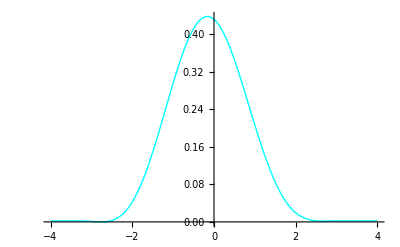

```mathematica
Plot[f13[x],{x,-4,4},PlotStyle->{Cyan,Thin}]
```

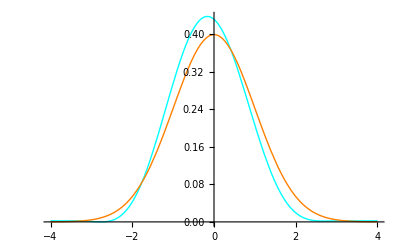

```mathematica
Plot[{f13[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Cyan,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL13= N[Integrate[F[x]*Log[F[x]/f13[x]],{x,-4,4}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.75012}. NIntegrate obtained 0.0510558 and 0.0000521339 for the integral and error estimates.

0.0510558

```mathematica
(*Verosimilitud*)
```

```mathematica
x13=Log[f13[datos]]
```

{-0.890426,-0.830901,-2.0904,-2.55885,-6.32908,-1.60656,-1.31888,-0.876223,-0.86438,-2.25971,-0.847406,-0.885506,-1.49287,-1.06919,9972,-1.16002,-0.902202,-1.7315,-0.843399,-1.67758,-1.08864,-0.91694,-1.70889,-0.851529,-1.35294,-1.38386,-0.967567,-1.51803,-0.853114}
 |  |  |  |

```mathematica
V13=Apply[Plus,x13]
```

-14648.8

```mathematica
(*BIC*)
```

```mathematica
BIC13 = -2*V13 + 14*Log[10000]
```

29426.6

### MOP DE GRADO 15

```mathematica
Integrate[x*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15+(34359738368 p)/17

```mathematica
Integrate[x^2*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15+(34359738368 o)/17

```mathematica
Integrate[x^3*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17+(549755813888 p)/19

```mathematica
Integrate[x^4*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17+(549755813888 o)/19

```mathematica
Integrate[x^5*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19+(8796093022208 p)/21

```mathematica
Integrate[x^6*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19+(8796093022208 o)/21

```mathematica
Integrate[x^7*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21+(140737488355328 p)/23

```mathematica
Integrate[x^8*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21+(140737488355328 o)/23

```mathematica
Integrate[x^9*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23+(2251799813685248 p)/25

```mathematica
Integrate[x^10*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23+(2251799813685248 o)/25

```mathematica
Integrate[x^11*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25+(36028797018963968 p)/27

```mathematica
Integrate[x^12*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25+(36028797018963968 o)/27

```mathematica
Integrate[x^13*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27+(576460752303423488 p)/29

```mathematica
Integrate[x^14*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27+(576460752303423488 o)/29

```mathematica
Integrate[x^15*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(34359738368 b)/17+(549755813888 d)/19+(8796093022208 f)/21+(140737488355328 h)/23+(2251799813685248 j)/25+(36028797018963968 l)/27+(576460752303423488 n)/29+(9223372036854775808 p)/31

```mathematica
Integrate[x^16*(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15),{x,-4,4}]
```

(34359738368 a)/17+(549755813888 c)/19+(8796093022208 e)/21+(140737488355328 g)/23+(2251799813685248 i)/25+(36028797018963968 k)/27+(576460752303423488 m)/29+(9223372036854775808 o)/31

```mathematica
F15[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_]=((128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15+(34359738368 p)/17-(Apply[Plus,datos])/10000)^2+((128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15+(34359738368 o)/17-(Apply[Plus,datos^2])/10000)^2+((2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17+(549755813888 p)/19-(Apply[Plus,datos^3])/10000)^2+((2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17+(549755813888 o)/19-(Apply[Plus,datos^4])/10000)^2+((32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19+(8796093022208 p)/21-(Apply[Plus,datos^5])/10000)^2+((32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19+(8796093022208 o)/21-(Apply[Plus,datos^6])/10000)^2+((524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21+(140737488355328 p)/23-(Apply[Plus,datos^7])/10000)^2+((524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21+(140737488355328 o)/23-(Apply[Plus,datos^8])/10000)^2+((8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23+(2251799813685248 p)/25-(Apply[Plus,datos^9])/10000)^2+((8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23+(2251799813685248 o)/25-(Apply[Plus,datos^10])/10000)^2+((134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25+(36028797018963968 p)/27-(Apply[Plus,datos^11])/10000)^2+((134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25+(36028797018963968 o)/27-(Apply[Plus,datos^12])/10000)^2+((2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27+(576460752303423488 p)/29-(Apply[Plus,datos^13])/10000)^2+((2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27+(576460752303423488 o)/29-(Apply[Plus,datos^14])/10000)^2+((34359738368 b)/17+(549755813888 d)/19+(8796093022208 f)/21+(140737488355328 h)/23+(2251799813685248 j)/25+(36028797018963968 l)/27+(576460752303423488 n)/29+(9223372036854775808 p)/31-(Apply[Plus,datos^15])/10000)^2+((34359738368 a)/17+(549755813888 c)/19+(8796093022208 e)/21+(140737488355328 g)/23+(2251799813685248 i)/25+(36028797018963968 k)/27+(576460752303423488 m)/29+(9223372036854775808 o)/31-(Apply[Plus,datos^16])/10000)^2
```

(-0.992368+(128 a)/3+(2048 c)/5+(32768 e)/7+(524288 g)/9+(8388608 i)/11+(134217728 k)/13+(2147483648 m)/15+(34359738368 o)/17)^2+(-2.9755+(2048 a)/5+(32768 c)/7+(524288 e)/9+(8388608 g)/11+(134217728 i)/13+(2147483648 k)/15+(34359738368 m)/17+(549755813888 o)/19)^2+(-14.7766+(32768 a)/7+(524288 c)/9+(8388608 e)/11+(134217728 g)/13+(2147483648 i)/15+(34359738368 k)/17+(549755813888 m)/19+(8796093022208 o)/21)^2+(-100.868+(524288 a)/9+(8388608 c)/11+(134217728 e)/13+(2147483648 g)/15+(34359738368 i)/17+(549755813888 k)/19+(8796093022208 m)/21+(140737488355328 o)/23)^2+(-860.688+(8388608 a)/11+(134217728 c)/13+(2147483648 e)/15+(34359738368 g)/17+(549755813888 i)/19+(8796093022208 k)/21+(140737488355328 m)/23+(2251799813685248 o)/25)^2+(-8625.74+(134217728 a)/13+(2147483648 c)/15+(34359738368 e)/17+(549755813888 g)/19+(8796093022208 i)/21+(140737488355328 k)/23+(2251799813685248 m)/25+(36028797018963968 o)/27)^2+(-96986.7+(2147483648 a)/15+(34359738368 c)/17+(549755813888 e)/19+(8796093022208 g)/21+(140737488355328 i)/23+(2251799813685248 k)/25+(36028797018963968 m)/27+(576460752303423488 o)/29)^2+(-1.18282×10^6+(34359738368 a)/17+(549755813888 c)/19+(8796093022208 e)/21+(140737488355328 g)/23+(2251799813685248 i)/25+(36028797018963968 k)/27+(576460752303423488 m)/29+(9223372036854775808 o)/31)^2+(0.0196627+(128 b)/3+(2048 d)/5+(32768 f)/7+(524288 h)/9+(8388608 j)/11+(134217728 l)/13+(2147483648 n)/15+(34359738368 p)/17)^2+(0.0566338+(2048 b)/5+(32768 d)/7+(524288 f)/9+(8388608 h)/11+(134217728 j)/13+(2147483648 l)/15+(34359738368 n)/17+(549755813888 p)/19)^2+(0.355927+(32768 b)/7+(524288 d)/9+(8388608 f)/11+(134217728 h)/13+(2147483648 j)/15+(34359738368 l)/17+(549755813888 n)/19+(8796093022208 p)/21)^2+(2.60393+(524288 b)/9+(8388608 d)/11+(134217728 f)/13+(2147483648 h)/15+(34359738368 j)/17+(549755813888 l)/19+(8796093022208 n)/21+(140737488355328 p)/23)^2+(17.1996+(8388608 b)/11+(134217728 d)/13+(2147483648 f)/15+(34359738368 h)/17+(549755813888 j)/19+(8796093022208 l)/21+(140737488355328 n)/23+(2251799813685248 p)/25)^2+(67.3493+(134217728 b)/13+(2147483648 d)/15+(34359738368 f)/17+(549755813888 h)/19+(8796093022208 j)/21+(140737488355328 l)/23+(2251799813685248 n)/25+(36028797018963968 p)/27)^2+(-763.198+(2147483648 b)/15+(34359738368 d)/17+(549755813888 f)/19+(8796093022208 h)/21+(140737488355328 j)/23+(2251799813685248 l)/25+(36028797018963968 n)/27+(576460752303423488 p)/29)^2+(-29202.8+(34359738368 b)/17+(549755813888 d)/19+(8796093022208 f)/21+(140737488355328 h)/23+(2251799813685248 j)/25+(36028797018963968 l)/27+(576460752303423488 n)/29+(9223372036854775808 p)/31)^2

```mathematica
Minimize[F15[a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l+4^12m-4^13n+4^14o-4^15p>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l+4^12m+4^13n+4^14o+4^15p>0},{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p}]
```

{4.16502×10^30,{a→0.82192,b→-0.118671,c→-0.00746223,d→-0.129551,e→-0.32813,f→-0.341904,g→0.201894,h→0.17913,i→-0.19768,j→-0.23643,k→0.534135,l→-0.549364,m→0.486294,n→-0.543029,o→-0.0289618,p→0.0352907}}

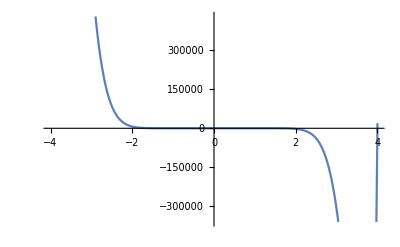

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15/.{a->0.8219202566209995,b->-0.11867064821065249,c->-0.0074622272426193015,d->-0.12955117214907536,e->-0.3281303788584625,f->-0.34190359916041285,g->0.20189386690752764,h->0.17913046979910874,i->-0.19767972486294197,j->-0.23643027786462978,k->0.5341350220565639,l->-0.5493642093858666,m->0.48629409669663193,n->-0.5430291765565324,o->-0.028961810440918195,p->0.03529066749972066},{x,-4,4}]
```

```mathematica
F151[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15/.{a->0.8219202566209995,b->-0.11867064821065249,c->-0.0074622272426193015,d->-0.12955117214907536,e->-0.3281303788584625,f->-0.34190359916041285,g->0.20189386690752764,h->0.17913046979910874,i->-0.19767972486294197,j->-0.23643027786462978,k->0.5341350220565639,l->-0.5493642093858666,m->0.48629409669663193,n->-0.5430291765565324,o->-0.028961810440918195,p->0.03529066749972066}
```

0.82192-0.118671 x-0.00746223 x^2-0.129551 x^3-0.32813 x^4-0.341904 x^5+0.201894 x^6+0.17913 x^7-0.19768 x^8-0.23643 x^9+0.534135 x^10-0.549364 x^11+0.486294 x^12-0.543029 x^13-0.0289618 x^14+0.0352907 x^15

```mathematica
Solve[F151[x]==0,Reals]
```

{{x→-4.07488},{x→0.96024},{x→3.99876}}

```mathematica
f[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15
```

a+b x+c x^2+d x^3+e x^4+f x^5+g x^6+h x^7+i x^8+j x^9+k x^10+l x^11+m x^12+n x^13+o x^14+p x^15

```mathematica
f[(0.9602401975916659+3.9987602371722986)/2]
```

a+2.4795 b+6.14792 c+15.2438 d+37.7969 e+93.7175 f+232.373 g+576.168 h+1428.61 i+3542.23 j+8782.97 k+21777.4 l+53997. m+133886. n+331969. o+823118. p

```mathematica
Minimize[F15[a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p],{a-4b+4^2c-4^3d+4^4e-4^5f+4^6g-4^7h+4^8i-4^9j+4^10k-4^11l+4^12m-4^13n+4^14o-4^15p>0,a+4b+4^2c+4^3d+4^4e+4^5f+4^6g+4^7h+4^8i+4^9j+4^10k+4^11l+4^12m+4^13n+4^14o+4^15p>0,
a+2.4795002173819825 b+6.147921327997298 c+15.243772269216626 d+37.79693665524406 e+93.71751265305066 f+232.3725929957378 g+576.1678948465468 h+1428.608420520532 i+3542.23488923439 j+8782.972177874712 k+21777.381424300253 l+53997.021975562806 m+133885.62772638767 n+331969.4430519014 o+823118.3062113652 p>0},{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p}]
```

{1.70517×10^31,{a→-0.151197,b→0.118206,c→0.21877,d→0.347366,e→0.170477,f→0.336862,g→0.591433,h→-0.648306,i→-0.524756,j→0.158066,k→0.436159,l→-0.240082,m→0.305262,n→0.10692,o→-0.0084273,p→-0.00749593}}

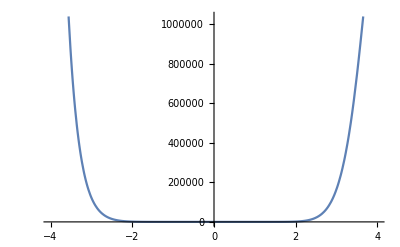

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15/.{a->-0.15119697762659076,b->0.11820616174610554,c->0.21877010658667198,d->0.3473657644876817,e->0.17047672588711626,f->0.33686190439873437,g->0.5914330758795238,h->-0.6483056117816184,i->-0.5247559426755708,j->0.15806576766805644,k->0.43615885375392743,l->-0.24008196435533424,m->0.30526171681008973,n->0.10692001180161967,o->-0.00842730291497387,p->-0.0074959307952774815},{x,-4,4}]
```

```mathematica
F152[x_]=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15/.{a->-0.15119697762659076,b->0.11820616174610554,c->0.21877010658667198,d->0.3473657644876817,e->0.17047672588711626,f->0.33686190439873437,g->0.5914330758795238,h->-0.6483056117816184,i->-0.5247559426755708,j->0.15806576766805644,k->0.43615885375392743,l->-0.24008196435533424,m->0.30526171681008973,n->0.10692001180161967,o->-0.00842730291497387,p->-0.0074959307952774815}
```

-0.151197+0.118206 x+0.21877 x^2+0.347366 x^3+0.170477 x^4+0.336862 x^5+0.591433 x^6-0.648306 x^7-0.524756 x^8+0.158066 x^9+0.436159 x^10-0.240082 x^11+0.305262 x^12+0.10692 x^13-0.0084273 x^14-0.00749593 x^15

```mathematica
Solve[F152[x]==0,Reals]
```

{{x→-0.832781},{x→0.460152},{x→4.2494}}

```mathematica
F152[0]
```

-0.151197

```mathematica
APN=-Integrate[F152[x],{x,-0.832780599963977,0.46015215854805236}]
```

0.178736

```mathematica
AT=Integrate[F152[x],{x,-4,-0.832780599963977}]-Integrate[F152[x],{x,-0.832780599963977,0.46015215854805236}]+Integrate[F152[x],{x,0.46015215854805236,4}]
```

2.25005×10^6

```mathematica
APN/AT
```

7.94364×10^-8

```mathematica
(*Como el área de la parte negativa ya es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación gráfica*)
```

```mathematica
FindMinimum[F152[x],{x,0}]
```

{-0.186704,{x→-0.527957}}

```mathematica
Integrate[a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15+0.18670402589939208/.{a->-0.15119697762659076,b->0.11820616174610554,c->0.21877010658667198,d->0.3473657644876817,e->0.17047672588711626,f->0.33686190439873437,g->0.5914330758795238,h->-0.6483056117816184,i->-0.5247559426755708,j->0.15806576766805644,k->0.43615885375392743,l->-0.24008196435533424,m->0.30526171681008973,n->0.10692001180161967,o->-0.00842730291497387,p->-0.0074959307952774815},{x,-4,4}]
```

2.25005×10^6

```mathematica
f15[x_]=(a+b*x+c*x^2+d*x^3+e*x^4+f*x^5+g*x^6+h*x^7+i*x^8+j*x^9+k*x^10+l*x^11+m*x^12+n*x^13+o*x^14+p*x^15+0.18670402589939208)/2.2500506249281373*^6/.{a->-0.15119697762659076,b->0.11820616174610554,c->0.21877010658667198,d->0.3473657644876817,e->0.17047672588711626,f->0.33686190439873437,g->0.5914330758795238,h->-0.6483056117816184,i->-0.5247559426755708,j->0.15806576766805644,k->0.43615885375392743,l->-0.24008196435533424,m->0.30526171681008973,n->0.10692001180161967,o->-0.00842730291497387,p->-0.0074959307952774815}
```

4.44434×10^-7 (0.035507+0.118206 x+0.21877 x^2+0.347366 x^3+0.170477 x^4+0.336862 x^5+0.591433 x^6-0.648306 x^7-0.524756 x^8+0.158066 x^9+0.436159 x^10-0.240082 x^11+0.305262 x^12+0.10692 x^13-0.0084273 x^14-0.00749593 x^15)

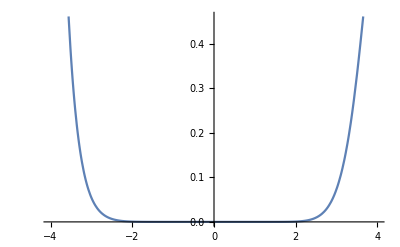

```mathematica
Plot[f15[x],{x,-4,4}]
```

### EVOLUCIÓN

```mathematica
(*Representación gráfica de todas juntas*)
```

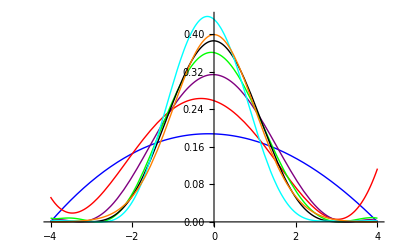

```mathematica
Plot[{f3[x],f5[x],f7[x],f9[x],f11[x],f13[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Red,Thin},{Purple,Thin},{Green,Thin},{Black,Thin},{Cyan,Thin},{Orange,Thin}}]
```

```mathematica
DKL = {{{3,KL3}},{{5,KL5}},{{7,KL7}},{{9,KL9}},{{11,KL11}},{{13,KL13}}}
```

{{{3,0.326031}},{{5,0.153667}},{{7,0.0347379}},{{9,0.0214025}},{{11,0.0108559}},{{13,0.0510558}}}

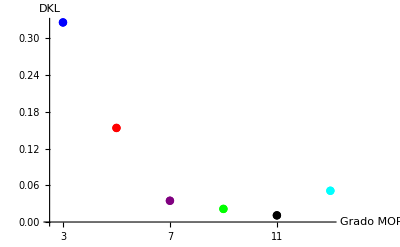

```mathematica
g1 =ListPlot[DKL,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","DKL"},AxesOrigin->{2.5,0},AxesStyle->Directive[Black, 12],Ticks->{{3,5,7,9,11,13}, Automatic}]
```

```mathematica
DKL1 = {{3,KL3},{5,KL5},{7,KL7},{9,KL9},{11,KL11},{13,KL13}}
```

{{3,0.326031},{5,0.153667},{7,0.0347379},{9,0.0214025},{11,0.0108559},{13,0.0510558}}

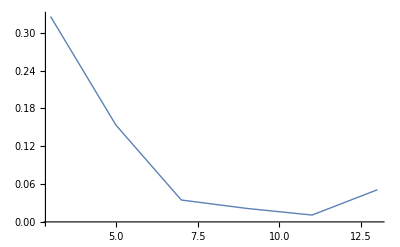

```mathematica
g2 = ListLinePlot[DKL1,PlotStyle->Thin]
```

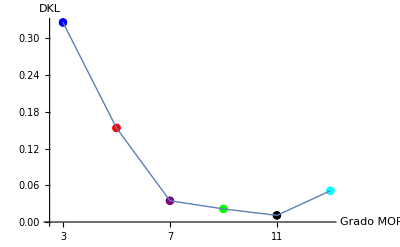

```mathematica
GrafDivMA=Show[g1,g2]
```

### GRÁFICO VEROSIMILITUDES

```mathematica
V = {{{3,V3}},{{5,V5}},{{7,V7}},{{9,V9}},{{11,V11}},{{13,V13}}}
```

{{{3,-17437.1}},{{5,-15674.5}},{{7,-14506.3}},{{9,-14393.4}},{{11,-14259.6}},{{13,-14648.8}}}

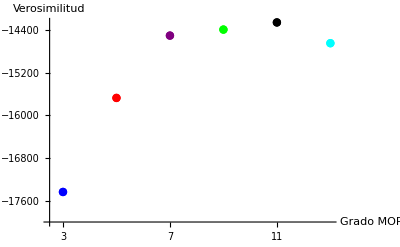

```mathematica
h1 =ListPlot[V,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-18000},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

```mathematica
V1 = {{3,V3},{5,V5},{7,V7},{9,V9},{11,V11},{13,V13}}
```

{{3,-17437.1},{5,-15674.5},{7,-14506.3},{9,-14393.4},{11,-14259.6},{13,-14648.8}}

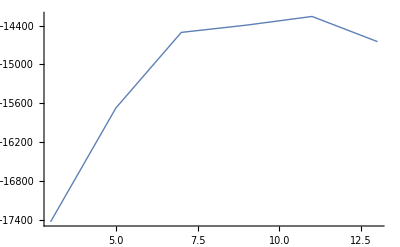

```mathematica
h2 = ListLinePlot[V1,PlotStyle->Thin,PlotRange->Full]
```

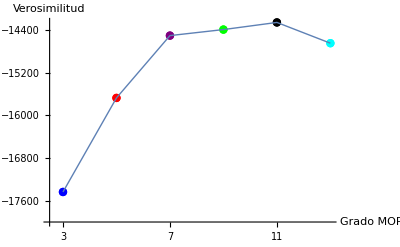

```mathematica
Show[h1,h2]
```

```mathematica
(*Gráfico verosimilitudes con otra muestra*)
```

```mathematica
SeedRandom[4321]
```

```mathematica
data2 = RandomVariate[NormalDistribution[0,1],10^4]
```

{0.747051,-1.23297,0.881603,-0.0754897,-0.631166,0.511102,2.26024,-0.792594,0.443516,0.444986,0.765234,-1.37841,-0.376238,1.56308,9972,0.186956,-1.66499,0.78839,-1.00169,-0.262297,-0.431108,-0.292597,-0.477039,-0.627549,0.884375,0.424782,-0.0453317,-0.8449,0.982922}
 |  |  |  |

```mathematica
y3 = Log[f3[data2]]
```

{-1.72277,-1.75227,-1.73947,-1.67301,-1.68811,-1.69951,-2.09934,-1.70013,-1.69422,-1.69432,-1.72487,-1.77634,-1.67625,-1.86768,-1.80894,-1.67631,-1.75083,-1.68594,-1.69295,-1.6797,-1.67734,-1.73583,-1.67442,-1.81808,-1.78351,-1.67535,9948,-1.79137,-1.68154,-1.73867,-1.69329,-1.69265,-1.73261,-1.72252,-1.86513,-1.69361,-1.67498,-1.68085,-1.67583,-1.67948,-1.83526,-1.72762,-1.72121,-1.67367,-1.67808,-1.67419,-1.67992,-1.68788,-1.73984,-1.69285,-1.67331,-1.70481,-1.75378}
 |  |  |  |

```mathematica
L3 = Apply[Plus,y3]
```

-17436.5

```mathematica
y5= Log[f5[data2]]
```

{-1.55087,-1.4947,-1.61224,-1.34662,-1.3538,-1.4638,-3.06607,-1.37731,-1.44334,-1.44377,-1.55864,-1.55229,-1.33652,-2.08933,-1.63204,-1.33656,-1.49129,-1.34996,-1.43837,-1.3836,-1.3726,-1.45626,-1.33594,-1.90166,-1.77359,-1.36241,9949,-1.39174,-1.60933,-1.43974,-1.43721,-1.58709,-1.54996,-2.07955,-1.36419,-1.36036,-1.3418,-1.365,-1.38259,-1.69749,-1.56878,-1.42293,-1.33648,-1.33822,-1.33603,-1.34049,-1.35339,-1.6136,-1.43801,-1.34945,-1.38709,-1.6646}
 |  |  |  |

```mathematica
L5= Apply[Plus,y5]
```

-15697.2

```mathematica
y7= Log[f7[data2]]
```

{-1.30863,-1.54582,-1.36757,-1.15965,-1.25188,-1.23,-2.85352,-1.30923,-1.213,-1.21334,-1.31598,-1.65338,-1.18999,-1.85453,9972,-1.16981,-1.91758,-1.32561,-1.40607,-1.17317,-1.20045,-1.177,-1.21039,-1.25076,-1.3689,-1.20871,-1.15909,-1.331,-1.41917}
 |  |  |  |

```mathematica
L7= Apply[Plus,y7]
```

-14508.8

```mathematica
y9= Log[f9[data2]]
```

{-1.24696,-1.5534,-1.33049,-1.01847,-1.13423,-1.13297,-3.32076,-1.21309,-1.10766,-1.10818,-1.25744,-1.71384,-1.05263,-1.99574,9972,-1.04044,-2.12134,-1.27115,-1.35,-1.03205,-1.06596,-1.03659,-1.07888,-1.13271,-1.33236,-1.10121,-1.01858,-1.24351,-1.40277}
 |  |  |  |

```mathematica
L9= Apply[Plus,y9]
```

-14358.

```mathematica
y11= Log[f11[data2]]
```

{-1.18976,-1.59548,-1.28478,-0.954238,-1.1101,-1.06355,-3.70703,-1.20524,-1.03642,-1.03696,-1.20159,-1.77239,-1.00665,-2.07432,9972,-0.96832,-2.20647,-1.21711,-1.36525,-0.9781,-1.02424,-0.984647,-1.04091,-1.10824,-1.28692,-1.02959,-0.953032,-1.24125,-1.36812}
 |  |  |  |

```mathematica
L11= Apply[Plus,y11]
```

-14244.9

```mathematica
y13= Log[f13[data2]]
```

{-1.27755,-1.48861,-1.42711,-0.830431,-0.945147,-1.0706,-5.0284,-1.04408,-1.02354,-1.02451,-1.29637,-1.70102,-0.850552,-2.622,9972,-0.891619,-2.24163,-1.32095,-1.22109,-0.831515,-0.864768,-0.835207,-0.879225,-0.943287,-1.43045,-1.01142,-0.833735,-1.08301,-1.5561}
 |  |  |  |

```mathematica
L13= Apply[Plus,y13]
```

-14688.7

```mathematica
L = {{{3,L3}},{{5,L5}},{{7,L7}},{{9,L9}},{{11,L11}},{{13,L13}}}
```

{{{3,-17436.5}},{{5,-15697.2}},{{7,-14508.8}},{{9,-14358.}},{{11,-14244.9}},{{13,-14688.7}}}

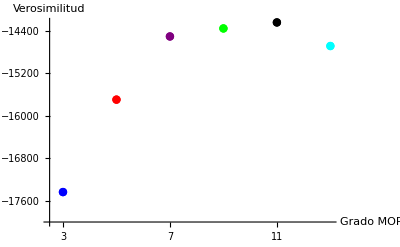

```mathematica
l1 =ListPlot[L,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]},{Magenta,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-18000},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13}, Automatic}]
```

```mathematica
L1={{3,L3},{5,L5},{7,L7},{9,L9},{11,L11},{13,L13}}
```

{{3,-17436.5},{5,-15697.2},{7,-14508.8},{9,-14358.},{11,-14244.9},{13,-14688.7}}

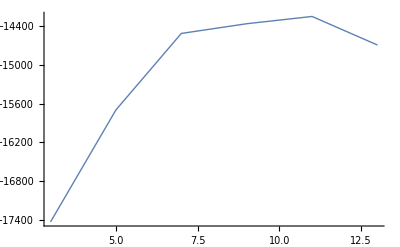

```mathematica
l2= ListLinePlot[L1,PlotStyle->Thin,PlotRange->Full]
```

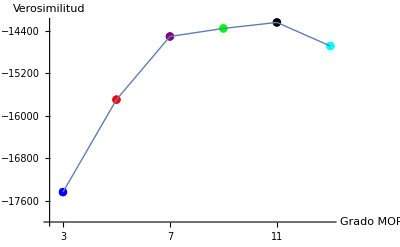

```mathematica
Show[l1,l2]
```

```mathematica
(*Gráficos DKL momentos y momentos aproximados*)
```

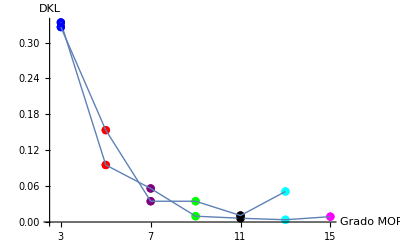

```mathematica
Show[GrafDivM,GrafDivMA]
```

### GRÁFICO BIC

```mathematica
B = {{{3,34910.94966000136}},{{5,31404.327948652084}},{{7,29086.264330364203}},{{9,28878.934472334644}},{{11,28629.80708221869}},{{13,29426.642181676183}}}
```

{{{3,34910.9}},{{5,31404.3}},{{7,29086.3}},{{9,28878.9}},{{11,28629.8}},{{13,29426.6}}}

```mathematica
B1 = {{3,34910.94966000136},{5,31404.327948652084},{7,29086.264330364203},{9,28878.934472334644},{11,28629.80708221869},{13,29426.642181676183}}
```

{{3,34910.9},{5,31404.3},{7,29086.3},{9,28878.9},{11,28629.8},{13,29426.6}}

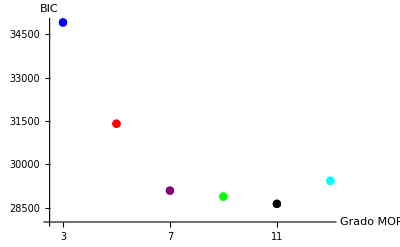

```mathematica
b1 =ListPlot[B,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,28000},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

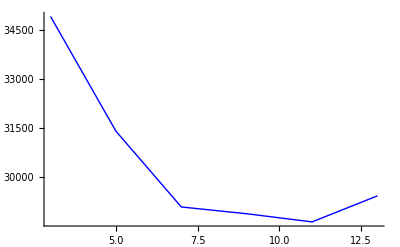

```mathematica
b2 = ListLinePlot[B1,PlotStyle->{Blue,Thin},PlotRange->Full]
```

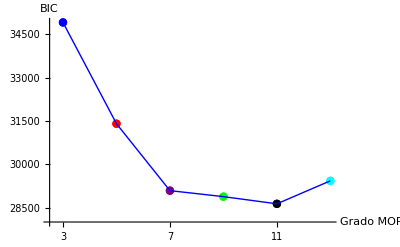

```mathematica
GrafBICNormalMuestra1MA = Show[b1,b2]
```

```mathematica
(*Gráfico BIC con otra muestra*)
```

```mathematica
BIC3N = -2*L3 + 4*Log[10000]
```

34909.8

```mathematica
BIC5N = -2*L5 + 6*Log[10000]
```

31449.7

```mathematica
BIC7N = -2*L7 + 8*Log[10000]
```

29091.2

```mathematica
BIC9N = -2*L9 + 10*Log[10000]
```

28808.

```mathematica
BIC11N = -2*L11 + 12*Log[10000]
```

28600.4

```mathematica
BIC13N = -2*L13 + 14*Log[10000]
```

29506.3

```mathematica
BN={{{3,34909.80376388302}},{{5,31449.688680481377}},{{7,29091.23781337348}},{{9,28808.030206166637}},{{11,28600.42293121605}},{{13,29506.26151987698}}}
```

{{{3,34909.8}},{{5,31449.7}},{{7,29091.2}},{{9,28808.}},{{11,28600.4}},{{13,29506.3}}}

```mathematica
B1N={{3,34909.80376388302},{5,31449.688680481377},{7,29091.23781337348},{9,28808.030206166637},{11,28600.42293121605},{13,29506.26151987698}}
```

{{3,34909.8},{5,31449.7},{7,29091.2},{9,28808.},{11,28600.4},{13,29506.3}}

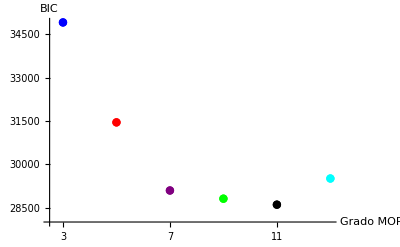

```mathematica
b1N = ListPlot[BN,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]},{Purple,Thin,PointSize[0.015]},{Green,Thin,PointSize[0.015]},{Black,Thin,PointSize[0.015]},{Cyan,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","BIC"},AxesOrigin->{2.5,28000},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,5,7,9,11,13,15}, Automatic}]
```

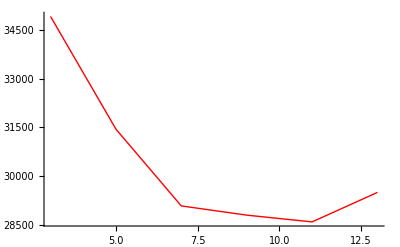

```mathematica
b2N = ListLinePlot[B1N,PlotStyle->{Red,Thin},PlotRange->Full]
```

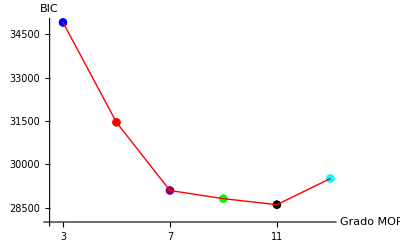

```mathematica
GrafBICNormalMuestra2MA = Show[b1N,b2N]
```

```mathematica
(*Comparación BIC dos muestras*)
```

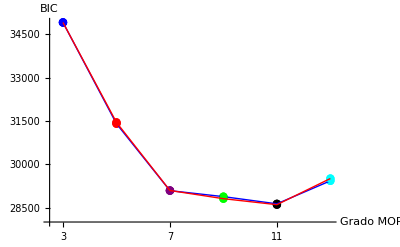

```mathematica
Show[GrafBICNormalMuestra1MA,GrafBICNormalMuestra2MA]
```

```mathematica
(*Momentos*)
```

```mathematica
Muestrales = Table[(Apply[Plus,datos^i])/10000,{i,1,16}]
```

{-0.0196627,0.992368,-0.0566338,2.9755,-0.355927,14.7766,-2.60393,100.868,-17.1996,860.688,-67.3493,8625.74,763.198,96986.7,29202.8,1.18282×10^6}

```mathematica
f3estimada = Table[Integrate[x^i*f3[x],{x,-4,4}],{i,1,16}]
```

{-0.0565282,3.20003,-0.387682,21.9433,-3.44659,195.054,-35.098,1986.02,-388.838,21999.2,-4563.07,258127.,-55839.1,3.15829×10^6,-705444.,3.98946×10^7}

```mathematica
f5estimada = Table[Integrate[x^i*f5[x],{x,-4,4}],{i,1,16}]
```

{-0.214228,2.4314,-0.3722,18.0736,5.76041,200.066,147.258,2586.1,2587.87,35710.1,41401.4,509342.,640025.,7.39975×10^6,9.7562×10^6,1.08785×10^8}

```mathematica
f7estimada = Table[Integrate[x^i*f7[x],{x,-4,4}],{i,1,16}]
```

{-0.0202427,1.38052,-0.0832794,5.08281,-0.492358,30.7448,-3.60781,267.7,-30.6735,2971.72,-291.604,37804.9,-3025.87,515659.,-33673.8,7.28879×10^6}

```mathematica
f9estimada = Table[Integrate[x^i*f9[x],{x,-4,4}],{i,1,16}]
```

{-0.00399441,1.15443,0.0318007,4.53788,0.11539,36.221,-0.0986012,413.15,0.00984634,5409.5,158.129,74706.2,5034.73,1.05746×10^6,111366.,1.51846×10^7}

```mathematica
f11estimada = Table[Integrate[x^i*f11[x],{x,-4,4}],{i,1,16}]
```

{-0.0116598,0.942792,-0.0348258,2.32569,-0.153855,8.76275,-0.888228,45.46,-6.42989,320.977,-56.7737,3001.7,-588.686,34437.4,-6856.64,445886.}

```mathematica
f13estimada = Table[Integrate[x^i*f13[x],{x,-4,4}],{i,1,16}]
```

{-0.131658,0.806149,-0.241704,2.18544,-0.585432,13.4367,-1.43742,136.402,-2.29363,1695.95,4.67867,22735.3,-0.200017,315283.,-1875.89,4.45919×10^6}

```mathematica
f15estimada =  Table[Integrate[x^i*f15[x],{x,-4,4}],{i,1,16}]
```

{-0.994392,13.6923,-15.1113,191.387,-228.932,2717.89,-3466.29,39084.3,-52520.4,567795.,-796852.,8.31834×10^6,-1.21101×10^7,1.22731×10^8,-1.8437×10^8,1.82176×10^9}

```mathematica
Table[{Integrate[x^i*f11[x],{x,-4,4}],Integrate[x^i*f13[x],{x,-4,4}],Integrate[x^i*f15[x],{x,-4,4}]},{i,1,16}]
```